ChemTools`DVR`Package

⌈Management⌋

$ChemDVRManager::usage="Manager interface for ChemDVR things";
ChemDVRDirectory::usage="Directory finder";
ChemDVRFile::usage=
	"Simple combination of FileNameJoin and ChemDVRDirectory";
ChemDVRPotentials::usage=
	"Lists all matching files in ChemDVRDirectory["PotentialEnergy"]";
$ChemDVRPotentials::usage="Alias for ChemDVRPotentials["*@.@*"]";

ChemDVRCreate::usage="OOP constructor for a ChemDVR";
ChemDVRAssociation::usage="Returns the base association for the instance";

ChemDVRSave::usage="Saves various ChemDVR components";
ChemDVRClear::usage="Clears saved ChemDVR components";

ChemDVRClass::usage="Template interface for a ChemDVR";
ChemDVRClasses::usage="Lists the available classes";
ChemDVRNewClass::usage="Opens up a template notebook for a new class";

ChemDVRBegin::usage="Wrapper for all BeginPackage stuff";
ChemDVREnd::usage="Wrapper for all EndPackage stuff";
$ChemDVRLoaded::usage="The set of packages loaded already";
ChemDVRNeeds::usage="Needs type loader for stuff";
ChemDVRReload::usage="Reloads a ChemDVR file";

⌈Defaults⌋

ChemDVRDefaultFormatGrid::usage="";
ChemDVRDefaultGrid::usage=
	"Default DVR grid function";
ChemDVRDefaultNamedGrid::usage="";
ChemDVRDirectProductGrid::usage=
	"Creates a direct product grid from two grid functions";
ChemDVRDirectProductKineticEnergy::usage=
	"Creates a direct product ke from two ke functions";
ChemDVRKroneckerProductKineticEnergy::usage=
	"Calculates the kinetic energy as a Kronecker product";
ChemDVRDefaultKineticEnergy::usage=
	"Calculates the kinetic energy as a product of kes"
ChemDVRDefaultNamedPotential::usage="";
ChemDVRDefaultPotentialEnergy::usage="";
ChemDVRDefaultWavefunctions::usage="";
ChemDVRDefaultPlot::usage="";
ChemDVRDefaultGridWavefunctions::usage="";
ChemDVRDefaultInterpolatingWavefunctions::usage="";
ChemDVRDefaultExpectationValues::usage="";
ChemDVRDefaultOperatorMatrix::usage="";

⌈Usage⌋

ChemDVRDimension::usage=
	"Returns the dimension of a ChemDVR object";
ChemDVRGrid::usage=
	"Returns the grid used in ChemDVR calculations";
ChemDVRKineticEnergy::usage=
	"Returns the kinetic energy used in ChemDVR calculations";
ChemDVRPotentialEnergy::usage=
	"Returns the potential energy used in ChemDVR calculations";
ChemDVRWavefunctions::usage=
	"Returns the wavefunctions computed in ChemDVR calculations";
ChemDVRGridWavefunctions::usage=
	"Returns the wavefunction imposed on the grid";
ChemDVRInterpolatingWavefunctions::usage=
	"Returns the wavefunctions interpolating over a grid";
ChemDVRExpectationValues::usage=
	"Returns the expectation values of a set of functions";
ChemDVROperatorMatrix::usage=
	"Returns the cross-state expectation matrix of a set of states->function specs";
ChemDVRView::usage="Displays the wavefunctions from a ChemDVR run";

ChemDVRNotebook::usage=
	"Opens a notebook for playing with a single ChemDVR instance";

Begin["`Private`"];

⌈Management⌋

⌈KeyWords⌋

$dvroot="Root";
$dvalt="ExtraDirs";
$dvrinst="Instances";
$dvrke="KineticEnergy";
$dvrpe="PotentialEnergy";
$dvrwf="Wavefunctions";
$dvrgr="Grid";
$dvrgrwf="GridWavefunctions";
$dvrintwf="InterpolatingWavefunctions";
$dvrexv="ExpectationValues";
$dvrexm="OperatorMatrix";
$dvrvw="View";

⌈Manager⌋

If[!MatchQ[$ChemDVRManager,_Association],
	$ChemDVRManager=
		<|
			"Directories"→
				<|
					$dvroot→ChemExtensionDir["DVR"],
					$dvalt→
						Map[
							FileNameJoin[{#, "DVR"}]&,
							{$ChemExtensionsApp, $ChemExtensionsDev}
							],
					"Classes"→"Classes",
					$dvrinst→$dvrinst,
					$dvrpe→$dvrpe,
					$dvrke→$dvrke,
					$dvrwf→$dvrwf
					|>,
			"Objects"→
				<|
					|>,
			"Settings"→
				<|
					"Load"<>$dvrke→False,
					"Save"<>$dvrke→False,
					"Load"<>$dvrpe→False,
					"Save"<>$dvrpe→False,
					"Load"<>$dvrwf→False,
					"Save"<>$dvrwf→False
					|>
			|>
	];

⌈Directory⌋

$ChemDVRRoot:=
	$ChemDVRManager["Directories", $dvroot];
$ChemDVRPath:=
	Prepend[
		$ChemDVRManager["Directories", $dvalt],
		$ChemDVRRoot
		]

Options[ChemDVRDirectory]=
	{
		"Root":>$ChemDVRRoot,
		"Path":>$ChemDVRPath
		};
ChemDVRDirectory[
	dSpec_?(KeyMemberQ[$ChemDVRManager["Directories"],#]&),
	alt:True|False:False,
	ops:OptionsPattern[]
	]:=
	With[{d=$ChemDVRManager["Directories", dSpec]},
		If[!alt,
			If[Not@DirectoryQ@ExpandFileName@d,
				(
					If[Not@DirectoryQ@#,
						CreateDirectory[#, CreateIntermediateDirectories→True]
						];
					#
					)&@
						FileNameJoin@{OptionValue["Root"], dSpec},
				d
				],
			FileNameJoin@{#,dSpec}&/@
				OptionValue["Path"]
			]
		];

⌈File⌋

ChemDVRFile//Clear

Options[ChemDVRFile]=
	Options@ChemDVRDirectory;
ChemDVRFile[
	dSpec_String?(KeyMemberQ[$ChemDVRManager["Directories"],#]&),
	fspec__String,
	o:OptionsPattern[]
	]:=
	With[
		{
			ops=
				FileNameJoin@{#,fspec}&/@
					ChemDVRDirectory[dSpec, True, o]
			},
		SelectFirst[ops, FileExistsQ, Last@ops]
		];
ChemDVRFile[
	dSpec_String?(KeyMemberQ[$ChemDVRManager["Directories"],#]&),
	ChemDVRObject[uuid_]
	]:=
	ChemDVRFile[
		dSpec,
		uuid<>If[MatchQ[dSpec,$dvrke|$dvrpe|$dvrwf],".mx",".m"]
		]
ChemDVRFile[ChemDVRObject[uuid_]]:=
	ChemDVRFile[$dvrinst,uuid<>".m"];

⌈Potentials⌋

ChemDVRPotentials[
	pat:_?StringPattern`StringPatternQ:"*@.@*",
	nameTake:True|False:True
	]:=
	If[nameTake,Map@FileNameTake,Identity]@
		FileNames[pat,ChemDVRDirectory[$dvrpe]];

⌈Create⌋

ChemDVRCreate::norng="No range function provided";
ChemDVRCreate::nogrid="No grid function provided";
ChemDVRCreate::noke="No kinetic energy function provided";
ChemDVRCreate::nope="No potential energy function provided";
ChemDVRCreate::novw="No view function provided";

ChemDVRCreate[a_Association]:=
	Block[{dvrAssoc=a},
		If[KeyMemberQ[a,"Class"],
			ChemDVRClass@a["Class"]];
		If[!KeyMemberQ[dvrAssoc,"UUID"],
			dvrAssoc["UUID"]=CreateUUID["ChemDVR-"]
			];
		If[!KeyMemberQ[dvrAssoc,"Name"],
			dvrAssoc["Name"]="ChemDVR Instance"
			];
		(*MapThread[
			If[!KeyMemberQ[dvrAssoc,#],
				Replace[#2,Hold[m_]:>
					Message[m]];
				dvrAssoc[#]=None;
				]&,{
			{},
			Thread@
				Hold[
					{
						}
					]
			}];*)
		(*If[!KeyMemberQ[dvrAssoc,"Points"],
			dvrAssoc["Points"]=
				ConstantArray[10, Length@dvrAssoc["Range"]]
			];*)
		If[!KeyMemberQ[dvrAssoc, $dvrgr],
			dvrAssoc[$dvrgr]=
				ChemDVRDefaultGrid
			];
		If[!KeyMemberQ[dvrAssoc, $dvrke],
			dvrAssoc[$dvrke]=
				ChemDVRDefaultKineticEnergy
			];
		If[!KeyMemberQ[dvrAssoc, $dvrpe],
			dvrAssoc[$dvrpe]=
				ChemDVRDefaultPotentialEnergy
			];
		If[!KeyMemberQ[dvrAssoc, $dvrwf],
			dvrAssoc[$dvrwf]=
				ChemDVRDefaultWavefunctions
			];
		If[!KeyMemberQ[dvrAssoc, $dvrvw],
			dvrAssoc[$dvrvw]=
				ChemDVRDefaultPlot
			];
		If[!KeyMemberQ[dvrAssoc, $dvrgrwf],
			dvrAssoc[$dvrgrwf]=
				ChemDVRDefaultGridWavefunctions
			];
		If[!KeyMemberQ[dvrAssoc, $dvrintwf],
			dvrAssoc[$dvrintwf]=
				ChemDVRDefaultInterpolatingWavefunctions
			];
		If[!KeyMemberQ[dvrAssoc, $dvrexv],
			dvrAssoc[$dvrexv]=
				ChemDVRDefaultExpectationValues
			];
		If[!KeyMemberQ[dvrAssoc, $dvrexm],
			dvrAssoc[$dvrexm]=
				ChemDVRDefaultOperatorMatrix
			];
		If[!KeyMemberQ[dvrAssoc,"FormatGrid"],
			dvrAssoc["FormatGrid"]=
				ChemDVRDefaultFormatGrid
			];
		$ChemDVRManager["Objects",dvrAssoc["UUID"]]=
			dvrAssoc;
		ChemDVRObject[dvrAssoc["UUID"]]
		];

ChemDVRCreate::nodvr="No ChemDVR found at ``";
ChemDVRCreate[dvr_String?FileExistsQ]:=
	With[{a=Get@dvr},
		If[AssociationQ@a,
			ChemDVRCreate@a,
			Message[ChemDVRCreate::nodvr,dvr];
			$Failed
			]
		];
ChemDVRCreate[dvr_String?(Not@*FileExistsQ)]:=
	With[{f=ChemDVRFile[$dvrinst,StringTrim[dvr,".m"]<>".m"]},	
		If[FileExistsQ@f,
			ChemDVRCreate@f,
			Message[ChemDVRCreate::nodvr,f]
			]
		];

⌈Save⌋

ChemDVRSave//Clear

Options[ChemDVRSave]=
	Options@ChemDVRFile;
ChemDVRSave[
	$dvrinst,
	name_String,
	a_Association,
	o:OptionsPattern[]
	]:=
	Block[{$ContextPath={"System`"}},
		Export[ChemDVRFile[$dvrinst, name, o],a]
		];
ChemDVRSave[
	prop:$dvrke|$dvrpe|$dvrwf, 
	name_String, 
	mx_List?MatrixQ,
	o:OptionsPattern[]
	]:=
	Export[	
		ChemDVRFile[prop, name, o],
		mx
		];

ChemDVRSave[
	Optional[$dvrinst,$dvrinst],
	ChemDVRObject[uuid_],
	o:OptionsPattern[]
	]:=
	ChemDVRSave[
		$dvrinst,
		uuid<>".m",
		$ChemDVRManager["Objects",uuid],
		o
		];
ChemDVRSave[
	prop:$dvrke|$dvrpe|$dvrwf, 
	ChemDVRObject[uuid_],
	mx_List?MatrixQ,
	o:OptionsPattern[]
	]:=
	ChemDVRSave[
		prop,
		uuid<>".mx",
		mx,
		o
		];

⌈Clear⌋

Options[ChemDVRClear]=
	Options@ChemDVRFile;
ChemDVRClear[prop:$dvrinst|$dvrke|$dvrpe|$dvrwf, name_String,
	ops:OptionsPattern[]
	]:=
	Quiet@DeleteFile@ChemDVRFile[prop,name, ops];

ChemDVRClear[
	prop:$dvrinst|$dvrke|$dvrpe|$dvrwf,$dvrinst,
	ChemDVRObject[uuid_],
	ops:OptionsPattern[]
	]:=
	ChemDVRClear[prop,
		uuid<>".m",
		ops
		];

⌈Defaults⌋

⌈FormatGrid⌋

ChemDVRDefaultFormatGrid[grid_,points_,___]:=
	grid;

⌈DefaultGridPointList⌋

Options[ChemDVRDefaultGridPointList]=
	{
		"GridPrepFunction"→Identity
		};
ChemDVRDefaultGridPointList[grid_, o:OptionsPattern[]]:=
	With[{dims=Dimensions[grid]},
		If[Depth@grid<=3,
			OptionValue["GridPrepFunction"]@grid,
			Flatten[
				OptionValue["GridPrepFunction"]@grid,
				Depth[grid]-3
				]
			]
		];

⌈ChemDVRDirectProductGrid⌋

⌈Alas this is best implemented procedurally owing to lack of FoldTuple⌋

chemDVRComputeGrid[fn_, pt_, reg_, opts:OptionsPattern[]]:=
	fn[pt, reg, FilterRules[{opts}, Options[fn]]]

ChemDVRDirectProductGrid[{grids__}]:=
		Outer[List, grids];
ChemDVRDirectProductGrid[
	fns_,
	pts_,
	regions_,
	opts:OptionsPattern[]
	]:=
	ChemDVRDirectProductGrid@
		MapThread[
			#[#2, #3, FilterRules[{opts}, Options[#]]]&,
			{
				fns,
				pts,
				regions
				}
			]

⌈ChemDVRDefaultGrid⌋

⌈ChemDVRDefaultNamedGrid⌋

⌈RegularSubdivision⌋

ChemDVRDefaultNamedGrid[
	"RegularSubdivision", 
	pt_Integer, {min_, max_}
	]:=
	Subdivide@@Flatten@{min, max, pt-1};

⌈InteriorSubdivision⌋

ChemDVRDefaultNamedGrid[
	"InteriorSubdivision", 
	pt_Integer, {min_, max_}
	]:=
	(max-min)/(pt+1)*Range[pt];

⌈AzimuthalSubdivision⌋

ChemDVRDefaultNamedGrid[
	"AzimuthalSubdivision", 
	pt_Integer, {min_, max_}
	]:=
	DeleteDuplicatesBy[Mod[#,2π]&]@
		ChemDVRDefaultNamedGrid[
			"RegularSubdivision", 
			pt, {min, max}
			]

⌈PolarSubdivision⌋

ChemDVRDefaultNamedGrid[
	"PolarSubdivision", 
	pt_Integer, {min_, max_}
	]:=
	DeleteDuplicatesBy[Mod[#, π]&]@
		ChemDVRDefaultNamedGrid[
			"RegularSubdivision", 
			pt, {min, max}
			]

⌈ChemDVRDefaultGrid⌋

⌈

	TODO: 
		include default grids; 
		allow for easy specification in DVR template files;
		handle NonCommutativeMultiply for direct product grids;
		handle arbitrary op matrix el func for determining change of basis;

⌋

ChemDVRRun::grdimfn=
	"Dimensions of grid (``) and number of grid types (``) don't match";
ChemDVRRun::ungrid=
	""GridType" `` not known";

Options[ChemDVRDefaultGrid]=
	{
		"GridType"→"RegularSubdivision"
		};
ChemDVRDefaultGrid[
	pts_,
	regions_,
	ops:OptionsPattern[]
	]:=
	With[
		{
			gfs=
				List@@
					Replace[
						OptionValue["GridType"], 
							s_?AtomQ:>ConstantArray[s, Length@pts]
						]
			},
		If[Length@Flatten[{gfs}, 1]=!=Length@pts, 
			Message[ChemDVRRun::grdimfn, Length@pts, Length@Flatten[{gfs}, 1]];
			Throw[$Failed]
			];
		MapThread[
			Switch[#,
				_String,
					Replace[ChemDVRDefaultNamedGrid[#, #2, #3],
						ChemDVRDefaultNamedGrid[s_, __]:>
							(
								Message[ChemDVRRun::ungrid, s];
								Throw[$Failed]
								)
						],
				_,
					#[#2, #3]
				]&,
			{
				gfs,
				pts,
				regions
				}
			]//
			Replace[
				{
					{l_}:>l,
					l:{__}:>ChemDVRDirectProductGrid[l]
					}
				]
		]

⌈NamedPotential⌋

ChemDVRObject::nonpot="Named potential `` unknown";

ChemDVRDefaultNamedPotential//Clear

⌈HarmonicOscillator⌋

ChemDVRDefaultNamedPotential["HarmonicOscillator", ops___?OptionQ]:=
	With[
		{
			k=Lookup[{ops}, "ForceConstant", 1/2],
			re=Lookup[{ops}, "EquilibriumBondLength", 0]
			},
		Norm[k*(#-re)^2]&
		];

⌈MorseOscillator⌋

ChemDVRDefaultNamedPotential["MorseOscillator", ops___?OptionQ]:=
	With[
		{
			de=Lookup[{ops}, "DissociationEnergy", 1],
			a=Lookup[{ops}, "α", 1],
			re=Lookup[{ops}, "EquilibriumBondLength", 0]
			},
		Norm[(de*(1-Exp[-a*(#-re)])^2)]&
		];

⌈HinderedRotor⌋

ChemDVRDefaultNamedPotential["HinderedRotor", ops___?OptionQ]:=
	With[
		{
			w=Lookup[{ops}, "WellNumber", 3],
			d=Lookup[{ops}, "WellDepth", 5.]
			},
		Norm[d*Cos[w/2*#]]&
		];

⌈Fallback⌋

ChemDVRDefaultNamedPotential[name_String, ops___?OptionQ]:=
	If[FileExistsQ[name]||MemberQ[ChemDVRPotentials[], name],
		name,
		With[
			{
				pe=PhysicalSystemData[name, "PotentialEnergy"],
				crds=PhysicalSystemData[name, "Coordinates"],
				vars=PhysicalSystemData[name, "Variables"]
				},
			If[MissingQ@pe||MissingQ@crds,
				Message[ChemDVRObject::nonpot, name];
				Throw[$Failed],
				With[
					{
						potExpr=
							pe/.
								Join[
									MapIndexed[
										Sequence@@
											{#→Apply[Slot, #2], #[___]→Apply[Slot, #2]}&,
										crds
										], 
									Flatten@
										Join[
											{ops}, 
											Replace[
												Flatten@{ops},
												(s_String→v_):>
													Sequence@@{
														QuantityVariable[_, s]→v, 
														QuantityVariable[s, _]→v
														},
												1
												]
											],
									Thread[vars→1]
									]
							},
					Function[potExpr]
					]
				]
			]
		];
ChemDVRDefaultNamedPotential[e___]:=
	(Message[ChemDVRObject::nonpot, {e}];Throw[$Failed])

⌈ChemDVRDefaultPotentialEnergy⌋

ChemDVRObject::badpot=
	"Potential function `` didn't return a numerical vector over the gridpoints";

⌈iChemDVRDefaultPotentialFunction⌋

⌈Need good symbolic representation for a direct product of potential functions, which can also work for the grid and for the kinetic energy too.⌋

iChemDVRDefaultPotentialFunction//Clear

iChemDVRDefaultPotentialFunction[s_String, ops___]:=
	ChemDVRDefaultNamedPotential[s, ops];
iChemDVRDefaultPotentialFunction[
	{s_String, op___?OptionQ},
	___
	]:=
	ChemDVRDefaultNamedPotential[s, op];
iChemDVRDefaultPotentialFunction[
	(NonCommutativeMultiply|List)[Repeated[Except[_?OptionQ].., {2, ∞}]], 
	ops___
	]:=
	Function[
		Evaluate@
			MapIndexed[#[Slot@@#2]&, 
				iChemDVRDefaultPotentialFunction[#, ops]&/@{a, b}
				]
		];
iChemDVRDefaultPotentialFunction[e_, ___]:=
	e

⌈ChemDVRDefaultPotentialEnergy⌋

Options[ChemDVRDefaultPotentialEnergy]=
	Join[
		{
			"PotentialFunction"→Automatic,
			Function→Automatic
			},
		Options@ChemDVRDefaultGridPointList
		];
ChemDVRDefaultPotentialEnergy[grid_, ops___?OptionQ]:=
	With[
		{
			pf=
				Replace[
					iChemDVRDefaultPotentialFunction[
						Lookup[Flatten@{ops}, "PotentialFunction", 
							Lookup[Options[ChemDVRDefaultPotentialEnergy], "PotentialFunction"]
							]
						],
					Except[_Function|_Symbol?(Length[DownValues[#]>0]&)]:>
						iChemDVRDefaultPotentialFunction[
							Lookup[Flatten@{ops}, Function, 
								Lookup[Options[ChemDVRDefaultPotentialEnergy], Function]
								]
							]
					],
			gp=
				ChemDVRDefaultGridPointList[grid, 
					FilterRules[{ops},
						Options@ChemDVRDefaultGridPointList
						]
					]
				},
		With[
			{
				gpVec=
					Replace[pf@gp, Except[_List]:>Map[pf, gp]]
				},
			If[!VectorQ@gpVec,
				Message[ChemDVRObject::badpot, pf];
				Throw[$Failed],
				SparseArray[Band[{1, 1}]->gpVec]
				]
			]
		];

⌈ChemDVRKroeneckerProductKineticEnergy⌋

⌈Many, many, many thanks to Henrik Schumacher for this wonderful implementation:
	https://mathematica.stackexchange.com/a/165953/38205⌋

⌈Imp⌋

⌈dvrKGetValues⌋

If[Length@OwnValues[dvrKGetValues]==0,
	dvrKGetValues := 
		dvrKGetValues=
			Compile[
				{
					{k1row, _Real, 1}, {blockvals, _Real, 2}, 
					{diagidx, _Integer, 1}, {i, _Integer}
					},
		   Block[{A},
		    A =
		    	Join[
			      Table[
								Compile`GetElement[k1row, k], 
								{l, 1, Dimensions[blockvals][[1]]}, 
								{k, 1, i}
								],
			      blockvals,
			      Table[
								Compile`GetElement[k1row, k], 
								{l, 1, Dimensions[blockvals][[1]]}, 
								{k, i + 2, Length[k1row]}
								],
			      2
			      ];
		    Do[
					A[[k, Compile`GetElement[diagidx, k] + i]] += 
						Compile`GetElement[k1row, i + 1], 
					{k, 1, Length[blockvals]}
					];
		    A
		    ],
		   RuntimeAttributes -> {Listable},
		   Parallelization -> True,
		   CompilationTarget -> "C",
		   RuntimeOptions -> "Speed"
		   ]
	]

⌈dvrKGetColumnIndices⌋

If[Length@OwnValues[dvrKGetColumnIndices]==0,
	dvrKGetColumnIndices := 
		dvrKGetColumnIndices=
			Compile[{
		    {blockci, _Integer, 3}, {diagci, _Integer, 
		     3}, {m, _Integer}, {n, _Integer}, {i, _Integer}
		    },
		   If[i > 0,
		    If[i < m - 1,
		     Join[
						diagci[[All, 1 ;; i]], 
						blockci + i n, 
						diagci[[All, i + 1 ;; m - 1]] + (n), 
						2
						],
		     Join[
						diagci[[All, 1 ;; i]], 
						blockci + i n, 
						2
						]
		     ],
		    Join[
		    	blockci + i n, 
		    	diagci[[All, i + 1 ;; m - 1]] + (n), 
		    	2
		    	]
		    ],
		   RuntimeAttributes -> {Listable},
		   Parallelization -> True,
		   CompilationTarget -> "C",
		   RuntimeOptions -> "Speed"
		   ]
	];

⌈dvrKToSparseArray⌋

dvrKToSparseArrayData[b_?MatrixQ] := {
  Partition[SparseArray[b]["ColumnIndices"], Dimensions[b][[2]]],
  b,
  Dimensions[b][[2]],
  Range[Dimensions[b][[2]]]
  }

dvrKToSparseArray[X_] := 
 With[{d1 = Dimensions[X[[1]]][[1]], d2 = Dimensions[X[[1]]][[2]]},
  SparseArray @@ {Automatic, {d1, d1}, 0,
    {1, {Range[0, d1 d2, d2], Flatten[X[[1]], 1]}, Flatten[X[[2]]]}}
  ]

⌈dvrKIteration⌋

dvrKIteration[X_, a_] := With[{
   m = Length[a],
   blockci = X[[1]],
   blockvals = X[[2]],
   n = X[[3]],
   diagidx = X[[4]]
   },
  With[{ran = Range[0, m - 1]},
   {
    Join @@ 
    	dvrKGetColumnIndices[blockci, 
    		Transpose[Partition[Partition[Range[(m - 1) n], 1], n]], 
    		m, 
    		n, 
    		ran
    		],
    Join @@ dvrKGetValues[a, blockvals, diagidx, ran],
    m n,
    Join @@ Outer[Plus, ran, diagidx]
    }
   ]
  ]

⌈ChemDVRDirectProductKineticEnergy⌋

ChemDVRKroeneckerProductKineticEnergy[keMats:{__List}]:=
	dvrKToSparseArray[
		Fold[dvrKIteration, 
			dvrKToSparseArrayData[keMats[[1]]], 
			Rest[keMats]
			]
		]

⌈ChemDVRDirectProductKineticEnergy⌋

chemDVRKeOptValue[k_, opts_, fns_]:=
	Lookup[opts, k,
		Lookup[Merge[Options/@fns, First], k,
			Lookup[Options[ChemDVRDirectProductKineticEnergy], k]
			]
		];

Options[ChemDVRDirectProductKineticEnergy]=
	Join[
		{
			"Masses"→Automatic,
			"HBars"→Automatic,
			"ScalingFactors"→Automatic,
			Precision→MachinePrecision
			},
		Options[ChemDVRDefaultGridPointList]
		];
ChemDVRDirectProductKineticEnergy[
	fns_,
	grid_,
	opts:OptionsPattern[]
	]:=
	With[
		{
			subgrids=
				Map[
					DeleteDuplicates, 
					Transpose@
						ChemDVRDefaultGridpointList[grid, 
							FilterRules[{opts}, Options[ChemDVRDefaultGridpointList]]
							]
					],
			masses=
				Replace[
					chemDVRKeOptValue["Masses", Flatten@{opts}, fns],
					{
						n_?NumericQ:>ConstantArray[n, Length@fns],
						{n__?NumericQ}:>Flatten[ConstantArray[n, Length@fns]][[;;Length@fns]],
						_:>ConstantArray[1, Length@fns]
						}
					],
			hbars=
				Replace[
					chemDVRKeOptValue["HBars", Flatten@{opts}, fns],
					{
						n_?NumericQ:>ConstantArray[n, Length@fns],
						{n__?NumericQ}:>Flatten[ConstantArray[n, Length@fns]][[;;Length@fns]],
						_:>ConstantArray[1, Length@fns]
						}
					],
			sfacs=
				Replace[
					chemDVRKeOptValue["ScalingFactors", Flatten@{opts}, fns],
					{
						n_?NumericQ:>ConstantArray[n, Length@fns],
						{n__?NumericQ}:>Flatten[ConstantArray[n, Length@fns]][[;;Length@fns]],
						_:>ConstantArray[1, Length@fns]
						}
					],
			prec=
				Replace[
					chemDVRKeOptValue[Precision, Flatten@{opts}, fns],
					Except[_?NumericQ|∞]→MachinePrecision
					]
			},
		ChemDVRKroneckerProductKineticEnergy[
			(*
				Compute the individual KEs to feed into Henriks Kronecker Product KE
			*)
			MapThread[
				With[{opt=Association@Options[fns]},
					If[KeyExistsQ[opt, "ScalingFactor"],
						Identity,
						With[{f=#5}, f*#&]
						]@
						If[KeyExistsQ[opt, Precision],
							Identity,
							N[#, prec]
							]@
							#[#2, 
								FilterRules[
									{"Mass"→#3, "HBar"→#4, "ScalingFactor"→#5, Precision→prec},
									Options[#]
									]
								]
					]&,
				{
					fns,
					subgrids,
					masses,
					hbars,
					sfacs
					}
				]
			]
		]

⌈ChemDVRDefaultKineticEnergy⌋

⌈iChemDVRDefaultKineticEnergy1D⌋

ChemDVRRun::badkeel=
	"Couldn't determine arguments for element function ``. \
Expected to take (i, j), (i, j, N) or (i, j, N, x[i], x[j])";

ChemDVRRun::badke=
	"Kinetic energy function returned non-numerical KE";

Options[iChemDVRDefaultKineticEnergy1D]=
	{
		"Mass"→1,
		"HBar"→1,
		"ScalingFactor"→1,
		Precision→MachinePrecision
		};
iChemDVRDefaultKineticEnergy1D[
	elementFunction_,
	gridpoints:{__?NumericQ},
	ops:OptionsPattern[]
	]:=
	Module[
		{
			gn=Length@gridpoints,
			dx=gridpoints[[2]]-gridpoints[[1]],
			hb=OptionValue["HBar"],
			m=OptionValue["Mass"],
			coeff,
			ke
			},
		coeff=
			If[NumericQ@OptionValue["ScalingFactor"],
				OptionValue["ScalingFactor"],
				1
				]*hb^2/(2m*dx^2);
		ke=
			Which[
				Quiet@NumericQ@elementFunction[1, 1],
					Table[coeff*elementFunction[i, j], {i, gn}, {j, gn}],
				Quiet@NumericQ@elementFunction[1, 1, gn],
					Table[coeff*elementFunction[i, j, gn], {i, gn}, {j, gn}],
				Quiet@NumericQ@elementFunction[1, 1, gn, gridpoints[[1]], gridpoints[[1]]],
					Table[
						coeff*elementFunction[i, j, gn, gridpoints[[i]], gridpoints[[j]]], 
						{i, gn}, {j, gn}],
				True,
					Message[ChemDVRRun::badkeel, elementFunction];
					Throw[$Failed]
				];
		If[!MatrixQ[ke, NumericQ], 
			ChemDVRRun::badke;
			Throw[$Failed]
			];
		If[OptionValue[Precision]===∞,
			ke,
			N[ke, OptionValue[Precision]]
			]
		];

⌈ChemDVRDefaultKineticEnergyElementFunction⌋

ChemDVRDefaultKineticEnergyElementFunction//Clear

⌈ColbertMillerCartesian⌋

ChemDVRDefaultKineticEnergyElementFunction["ColbertMillerCartesian"]:=
	Function[
		If[#==#2, 
			π^2/3, 
			2/(#-#2)^2
			]*((-1)^(#-#2))
		];

⌈ColbertMillerRadial⌋

ChemDVRDefaultKineticEnergyElementFunction["ColbertMillerRadial"]:=
	Function[
		If[#==#2, 
			π^2/3-1/#^2,
			2/(#-#2)^2-2/(#+#2)^2
			]*((-1)^(#-#2))
		];

⌈ColbertMillerPolar⌋

ChemDVRDefaultKineticEnergyElementFunction["ColbertMillerPolar"]:=
	Function[
		(#3/Pi)^2/2*
			If[#==#2,
				(2*#3^2+1)/3-1/(Sin[Pi*#/#3]&2),
				((-1)^(#-#2))/
					(Sin[(π*(#-#2))/(2*#3)]^2-Sin[(π*(#+#2))/(2*#3)]^2)
				]
		];

⌈MeyerAzimuthal⌋

ChemDVRDefaultKineticEnergyElementFunction["MeyerAzimuthal"]:=
	Function[
		If[#==#2,
			(#3^2/2+1)*1/6,
			((-1)^(#-#2))/
				(2*Sin[(π*(#-#2))/#3]^2)
			]
		];

⌈Fallback⌋

ChemDVRDefaultKineticEnergyElementFunction[___]:=
	(
		Message[ChemDVRRun::nokel, "Unknown kinetic energy element function ``"];
		Throw[$Failed]
		)

⌈ChemDVRDefaultKineticEnergy⌋

ChemDVRRun::kedimx=
	"Dimension of grid (``) doesn't match number of kinetic energy element\
 functions (``)";

Options[ChemDVRDefaultKineticEnergy]=
	Join[
		{
			"KineticEnergyElementFunction"→Automatic
			},
		Options[iChemDVRDefaultKineticEnergy]
		];
ChemDVRDefaultKineticEnergy[
	gridpoints_,
	ops:OptionsPattern[]
	]:=
	With[
		{
			keel=
				Replace[OptionValue["KineticEnergyElementFunction"],
					k:_Cross|_NonCommutativeMultiply:>List@@k
					]
				},
		Switch[keel,
			{Repeated[Except[_?OptionQ], {2, ∞}]},
				With[
					{
						subgrids=
							Replace[
								ChemDVRDefaultGridPointList[
									gridpoints, 
									FilterRules[{ops}, Options[ChemDVRDefaultGridPointList]]
									],
								l:{__List}:>
									Map[
										DeleteDuplicates, 
										Transpose@l
										]
								]
						},
					If[Length@subgrids=!=Length@keel,
						Message[ChemDVRRun::kedimx, Length@subgrids, Length@keel];
						Throw[$Failed]
						];
					ChemDVRKroeneckerProductKineticEnergy@
						MapThread[
							iChemDVRDefaultKineticEnergy1D[#, #2, 
								FilterRules[{ops}, Options[iChemDVRDefaultKineticEnergy1D]]
								]&,
							{
								keel,
								subgrids
								}
							]
					],
			_String,
				ChemDVRDefaultKineticEnergy[
					gridpoints,
					"KineticEnergyElementFunction"->
						ChemDVRDefaultKineticEnergyElementFunction[keel],
					ops
					],
			{_String, o___?OptionQ},
				ChemDVRDefaultKineticEnergy[
					gridpoints,
					"KineticEnergyElementFunction"->
						Apply[ChemDVRDefaultKineticEnergyElementFunction, keel],
					ops
					],
			{_},
				iChemDVRDefaultKineticEnergy1D[First@keel, gridpoints, 
					FilterRules[{ops}, Options[iChemDVRDefaultKineticEnergy1D]]
					],
			_,
				iChemDVRDefaultKineticEnergy1D[keel, gridpoints, 
					FilterRules[{ops}, Options[iChemDVRDefaultKineticEnergy1D]]
					]
			]
		]

⌈WavefunctionSelection⌋

chemDVRScaledWavefunctionSpan[s_, len_]:=
	Which[
		s>=1, 
			Sequence@@{},
		s==0,
			Sequence@@{},
		s<0,
			Ceiling[s*len];;,
		True,
			;;Floor[s*len] 
		]

Options[ChemDVRDefaultWavefunctionSelection]=
	{
		"WavefunctionSelection"→All
		};
ChemDVRDefaultWavefunctionSelection[wfs_, 
	sel:Except[_?OptionQ], ops:OptionsPattern[]]:=
	If[sel=!=All,
		wfs[[All, 
			Replace[sel,
				{
					i_Integer?Positive:>
						If[i>Length@wfs[[1]], All, ;;i],
					i_Integer?Negative:>
						If[-i>Length@wfs[[1]], All, i;;],
					Scaled[s_?NumericQ]:>
						chemDVRScaledWavefunctionSpan[s, Length@wfs[[1]]],
					Scaled[{min_?NumericQ, max_?NumericQ}]:>
						With[{minMax=Sort@{min, max}},
							Replace[
								{
									chemDVRScaledWavefunctionSpan[minMax[[1]], Length@wfs[[1]]],
									chemDVRScaledWavefunctionSpan[minMax[[2]], Length@wfs[[1]]]
									},
								{
									{}:>
										Sequence@@{},
									{M_;;, ;;m_}|
										{m_;;, M_;;}|
										{;;m_, ;;M_}:>m;;M,
									{e_}:>e
									}
								]
							]
					}
				]
			]],
		wfs
		];
ChemDVRDefaultWavefunctionSelection[wfs_, ops:OptionsPattern[]]:=
	ChemDVRDefaultWavefunctionSelection[wfs,
		OptionValue["WavefunctionSelection"]
		]

⌈ChemDVRDefaultWavefunctions⌋

ChemDVRRun::badham="The computed Hamiltonian is not a square numerical matrix";

Options[ChemDVRDefaultWavefunctions]=
	Join[
		Options@Eigensystem,
		{
			"NumberOfWavefunctions"→Automatic,
			"CorrectPhase"→True,
			"SortEnergies"→True
			}
		];
ChemDVRDefaultWavefunctions[T_,V_,ops:OptionsPattern[]]:=
	Module[
		{
			ham=T+V,
			nwfs=OptionValue["NumberOfWavefunctions"],
			sort=OptionValue["SortEnergies"]=!=False,
			rephase=OptionValue["CorrectPhase"]=!=False,
			wfns,
			phase
			},
		If[!SquareMatrixQ[ham]||!MatrixQ[ham, NumericQ],
			Message[ChemDVRRun::badham];
			Throw[$Failed]
			]; 
		wfns=
				If[sort, #[[{1,2},Ordering[First@#]]], #]&@
					Eigensystem[
						ham,
						Replace[nwfs,
							{
								Automatic:>
									If[Head@ham===SparseArray, 
										-Abs[Min@{Max@{Length@ham/10, 20}, Length@ham, 25}],
										Sequence@@{}
										],
								i_Integer:>-i,
								_:>Sequence@@{}
								}
							],
						Method→
							Replace[OptionValue[Method], 
								Automatic:>
									If[Head@ham===SparseArray, 
										Automatic,
										"FEAST"
										]
								],
						FilterRules[
							FilterRules[{ops},Alternatives@@Keys@Options@Eigensystem],
							Except[Method]
							]
						];
		If[rephase,
			phase=Sign@wfns[[2, Ordering[First@wfns][[1]]]];
			{First@wfns,phase*#&/@Last@wfns},
			wfns
			]
		];

⌈ChemDVRDefaultGridWavefunctions⌋

Options[ChemDVRDefaultGridWavefunctions]=
	Join[
		{
			"ReturnEnergies"→False
			},
		Options[ChemDVRDefaultWavefunctionSelection],
		Options[ChemDVRDefaultGridPointList]
		];
ChemDVRDefaultGridWavefunctions[grid_,wfs_, o:OptionsPattern[]]:=
	With[
		{
			coreGridPoints=
				ChemDVRDefaultGridPointList[grid, 
					FilterRules[{o}, Options@ChemDVRDefaultGridPointList]
					],
			wfns=
				ChemDVRDefaultWavefunctionSelection[
					wfs,
					FilterRules[{o}, Options[ChemDVRDefaultWavefunctionSelection]]
					],
			retE=TrueQ@OptionValue["ReturnEnergies"]
			},
		If[retE, 
			MapThread[
				#->Thread[{coreGridPoints,#2}]&,
				wfns
				],
			Map[Thread[{coreGridPoints,#}]&, wfns[[2]]]
			]
		];

⌈ChemDVRDefaultInterpolatingWavefunctions⌋

Options[ChemDVRDefaultInterpolatingWavefunctions]=
	Options@ChemDVRDefaultGridWavefunctions;
ChemDVRDefaultInterpolatingWavefunctions[
	grid_,
	wfs_,
	ops:OptionsPattern[]
	]:=
	With[
		{
			coreGridPoints=
				ChemDVRDefaultGridPointList[grid, 
					FilterRules[{ops}, Options@ChemDVRDefaultGridPointList]
					],
			wfns=
				ChemDVRDefaultWavefunctionSelection[
					wfs,
					FilterRules[{ops}, Options[ChemDVRDefaultWavefunctionSelection]]
					],
			retE=TrueQ@OptionValue["ReturnEnergies"]
			},
		If[retE, 
			MapThread[
				#->Interpolation@MapThread[Flatten@*List,{coreGridPoints,#2}]&,
				wfns
				],
			Map[Interpolation@MapThread[Flatten@*List,{coreGridPoints, #}]&, wfns[[2]]]
			]
		];

⌈ChemDVRDefaultExpectationValues⌋

⌈chemDVRCalcExpectationValue⌋

chemDVRCalcExpectationValueVec[func_, grid_]:=
	Replace[func@grid, 
		Except[_List?(Length[#]==Length@grid&)]:>Map[func, grid]
		];
chemDVRCalcExpectationValueVec[func_, grid_, wf_]:=
	Replace[func[grid, wf], 
		Except[_List?(Length[#]==Length@grid&)]:>
			MapThread[func, {grid, wf}]
		];
chemDVRCalcExpectationValue[func_Function, grid_, wfL_, wfR_]:=
	wfL.
		If[MemberQ[func, Slot[2], ∞],
			chemDVRCalcExpectationValueVec[func, grid, wfR],
			wfR*chemDVRCalcExpectationValueVec[func, grid]
			];
chemDVRCalcExpectationValue[func:Except[_Function], grid_, wfL_, wfR_]:=
	wfL.Replace[chemDVRCalcExpectationValueVec[func, grid, wfR],
		{__func}:>wfR*chemDVRCalcExpectationValueVec[func, grid]
		]

⌈ChemDVRDefaultExpectationValues⌋

Options[ChemDVRDefaultExpectationValues]=
	Options@ChemDVRDefaultGridWavefunctions;
ChemDVRDefaultExpectationValues[
	grid_,
	wfs_,
	evs_,
	ops:OptionsPattern[]
	]:=
	With[
		{
			coreGridPoints=
				ChemDVRDefaultGridPointList[grid, 
					FilterRules[{ops}, Options[ChemDVRDefaultGridPointList]]
					],
			exfns=
				Flatten@List@evs,
			wfns=
				ChemDVRDefaultWavefunctionSelection[
					wfs,
					FilterRules[{ops}, Options[ChemDVRDefaultWavefunctionSelection]]
					],
			retE=
				TrueQ@OptionValue["ReturnEnergies"]
			},
		If[retE, 
			wfns[[1]]→#&,
			Identity
			]@
				If[Not@ListQ@evs, Map[First], Identity]@
					Table[
						Map[
							chemDVRCalcExpectationValue[#, coreGridPoints, wf, wf]&,
							exfns
							],
						{wf, wfns[[2]]}
						]
		];

⌈ChemDVRDefaultOperatorMatrix⌋

Options[ChemDVRDefaultOperatorMatrix]=
	Options@ChemDVRDefaultExpectationValues;
ChemDVRDefaultOperatorMatrix[
	grid_,
	wfs_,
	evs_,
	ops:OptionsPattern[]
	]:=
	Module[
		{
			coreGridPoints=
				ChemDVRDefaultGridPointList[grid, 
					FilterRules[{ops}, Options[ChemDVRDefaultGridPointList]]
					],
			exfns=
				Flatten@List@evs,
			sels,
			wfns,
			retE=
				TrueQ@OptionValue["ReturnEnergies"]
			},
		{sels, exfns}=
			Transpose@
				Replace[exfns,
					{
						(sel_→fn_):>
							{sel, fn},
						fn_:>
							{OptionValue["WavefunctionSelection"], fn}
						},
					1
					];
		wfns=
			Map[ChemDVRDefaultWavefunctionSelection[wfs, #]&, sels];
		If[Length@sels==1, First, Identity]@
			MapThread[
				Block[
					{mx, eSet=#[[1]], wfSet=#[[2]], exFs=#2},
					If[retE, 
						Array[
							{eSet[[#]], eSet[[#2]]}&,
							{Length@wfSet, Length@wfSet}
							]→#&,
						Identity
						]@
					Table[
						With[{i=i, j=j, gr=coreGridPoints, wfL=wfSet[[i]], wfR=wfSet[[j]]},
							If[Not@ListQ@exFs,
								chemDVRCalcExpectationValue[
									exFs, 
									gr, 
									wfL, wfR
									],
								Map[
									chemDVRCalcExpectationValue[
										#, 
										gr, 
										wfL, wfR
										]&,
									exFs
									]
								]
							],
						{i, Length@wfSet},
						{j, Length@wfSet}
						]
					]&,
				{
					wfns,
					exfns
					}
				]
		];

⌈ChemDVRDefaultPlot⌋

⌈$ChemDVRDefaultPlotOptions⌋

$ChemDVRDefaultPlotOptions=
	DeleteDuplicatesBy[First]@
		Join[
			{
				"ZeroAxis"→True,
				"ShowEnergy"→True,
				"ShowPotential"→True,
				"PotentialStyle"→Automatic,
				"WavefunctionSelection"→Scaled[.25],
				"WavefunctionClipping"→10^-5,
				"WavefunctionScaling"→Scaled[.5],
				"WavefunctionShifting"→None,
				"WavefunctionRescaling"→None,
				"PotentialRescaling"→None,
				"PlotProbabilityDensity"→False,
				"PlotDisplayMode"->Manipulate,
				"PlotFunction"→Automatic,
				"CoordinateTransformation"→None,
				"PlotListStyle"→Automatic
				},
			Options[ChemDVRDefaultGridPointList],
			Options[ChemDVRDefaultWavefunctionSelection]
			]

⌈ChemDVRDefaultPlotOptionValue⌋

ChemDVRDefaultPlotOptionValue[opName_, ops_, f_:None, default_:Automatic]:=
	Lookup[Flatten@{ops}, opName,
		Lookup[Options[f], opName, 
			Lookup[$ChemDVRDefaultPlotOptions, opName, default]
			]
		]

⌈ChemDVRDefaultPlotGetShiftedScaledWavefunctions⌋

ChemDVRDefaultPlotGetShiftedScaledWavefunctions//Clear

⌈chemDVRDefaultPlotWavefunctionRescalingFunction⌋

chemDVRDefaultPlotWavefunctionRescalingFunction//Clear;
chemDVRDefaultPlotWavefunctionRescalingFunction[
	{min_?NumericQ, max_?NumericQ},
	_
	]:=
	Map[Rescale[#, MinMax[#], {min, max}]&];
chemDVRDefaultPlotWavefunctionRescalingFunction[
	Scaled[mm:{_?NumericQ, _?NumericQ}],
	pot_
	]:=
	With[{pmm=mm*MinMax[pot]},
		Map[Rescale[#, MinMax[#], pmm]&]
		];
chemDVRDefaultPlotWavefunctionRescalingFunction[
	Scaled[n_?NumericQ],
	pot_
	]:=
	chemDVRDefaultPlotWavefunctionRescalingFunction[
		Scaled[{0, n}],
		pot
		];
chemDVRDefaultPlotWavefunctionRescalingFunction[___]:=
	Identity

⌈ChemDVRDefaultPlotGetShiftedScaledWavefunctions⌋

ChemDVRDefaultPlotGetShiftedScaledWavefunctions[
	psi_,
	pot_,
	shift_,
	scale_,
	rescale_
	]:=
	With[
		{
			rescalePsi=
				chemDVRDefaultPlotWavefunctionRescalingFunction[rescale, pot][psi],
			shiftFactor=
				Replace[shift,
					Scaled[s_?NumericQ]:>
						s*Max@Abs[pot]
					],
			scaleFactor=
				Replace[scale,
					Scaled[s_?NumericQ]:>
						s*Max@Abs[pot]
					]
			},
		If[NumericQ@shiftFactor,
			If[NumericQ@scaleFactor, scaleFactor*shiftFactor, shiftFactor]+#,
			#
			]&@
			If[NumericQ@scaleFactor, 
				With[{maxPsi=Max[Abs[psi]]},
					MapThread[
						With[{minPsi=First@MinimalBy[#, Abs]},
							#2-scaleFactor*minPsi/maxPsi
							]&,
						{
							rescalePsi,
							scaleFactor*rescalePsi/maxPsi
							}
						]
					],
				rescalePsi
				]
		];

⌈ChemDVRDefaultPlotGetClippedWavefunctionSpec⌋

ChemDVRDefaultPlotGetClippedWavefunctionSpec[
	psi_,
	clip_?NumericQ
	]:=
	Map[#>=clip&, Abs[psi]]; 
ChemDVRDefaultPlotGetClippedWavefunctionSpec[
	psi_,
	Scaled[clip_?NumericQ]
	]:=
	ChemDVRDefaultPlotGetClippedWavefunctionSpec[
		psi,
		Rescale[clip, {0, 1}, MinMax[Abs@psi]]
		];
ChemDVRDefaultPlotGetClippedWavefunctionSpec[
	psi_,
	_
	]:=
	ConstantArray[True, Length@psi];

⌈ChemDVRDefaultPlotGetPlotPoints⌋

⌈Handle zero axes appropriately⌋

⌈Imp⌋

iChemDVRDefaultPlotGetPlotPoints[
	sel_,
	pot_,
	grid_,
	scaling_,
	shifting_,
	rescaling_,
	clip:_Scaled|_?NumericQ
	]:=
	With[
		{
			scaledPsi=
				ChemDVRDefaultPlotGetShiftedScaledWavefunctions[
					sel, pot, 
					shifting, scaling, rescaling
					]
			},
		MapThread[
			With[
				{
					pspec=ChemDVRDefaultPlotGetClippedWavefunctionSpec[#, clip]
					},
				MapThread[
					Flatten@*List,
					{
						Pick[grid, pspec], 
						Pick[#2, pspec]
						}
					]
				]&,
			{
				sel,
				scaledPsi
				}
			]
		];
iChemDVRDefaultPlotGetPlotPoints[
	sel_,
	pot_,
	grid_,
	scaling_,
	shifting_,
	rescaling_,
	clip:Except[_?NumericQ]
	]:=
	With[
		{
			scaledPsi=
				ChemDVRDefaultPlotGetShiftedScaledWavefunctions[
					sel, pot, 
					shifting, scaling, rescaling
					]
			},
		Map[
			MapThread[Flatten@*List, {grid, #}]&,
			scaledPsi
			]
		]

⌈potResc⌋

chemDVRDefaultPlotPotentialRescalingFunction[potResc_]:=
	Replace[potResc, 
		{
			{_?NumericQ, _?NumericQ}:>
				Function@Rescale[#, MinMax[#], potResc],
			Scaled[s:{_?NumericQ, _?NumericQ}]:>
				Function@
					With[{mm=MinMax[#]},
						Rescale[#, mm, s*mm]
						],
			Offset[
				off:_?NumericQ,
				scl:{_?NumericQ, _?NumericQ}
				]:>
				Function[
					off+Rescale[#, MinMax[#], scl]
					],
			Offset[
				off:_?NumericQ,
				Scaled[scl:{_?NumericQ, _?NumericQ}]
				]:>
				Function@
					With[{mm=MinMax[#]},
						off+If[scl=={1, 1}, #, Rescale[#, mm, scl*mm]]
						],
			Offset[
				Scaled[off:_?NumericQ],
				scl:{_?NumericQ, _?NumericQ}
				]:>
				Function@
					With[{mm=MinMax[#]},
						(off*First[mm])+Rescale[#, mm, scl*mm]
						],
			Offset[
				Scaled[off:_?NumericQ],
				Scaled[scl:{_?NumericQ, _?NumericQ}]
				]:>
				Function@
					With[{mm=MinMax[#]},
						(off*First[mm])+If[scl=={1, 1}, #, Rescale[#, mm, scl*mm]]
						],
			_->Identity
			}
		]

⌈Main⌋

Options[ChemDVRDefaultPlotGetPlotPoints]=
	$ChemDVRDefaultPlotOptions;
ChemDVRDefaultPlotGetPlotPoints[
	gridpoints_,
	psi_,
	pot_,
	showPot_,
	showEng_,
	transf_,
	ops:OptionsPattern[]
	]:=
	With[
		{
			scaling=
				OptionValue["WavefunctionScaling"],
			rescaling=
				OptionValue["WavefunctionRescaling"],
			clipping=
				OptionValue["WavefunctionClipping"],
			shift=
				OptionValue["WavefunctionShifting"],
			potResc=
				OptionValue["PotentialRescaling"],
			wfnsel=
				ChemDVRDefaultWavefunctionSelection[
					psi, 
					FilterRules[{ops}, 
						Options@ChemDVRDefaultWavefunctionSelection
						]
					],
			sqr=
				TrueQ["PlotProbabilityDensity"],
			gps=
				If[transf===None, 
					gridpoints, 
					Map[
						Replace[transf,
							chart_Rule:>
								Function[
									Evaluate@
										CoordinateTransform[chart, 
											Slot/@Range[Length[gridpoints[[1]]]]
											]
									]
							],
						gridpoints
						]
					],
				za=
					TrueQ@OptionValue["ZeroAxis"]
				},
		{
			If[TrueQ@showEng,
				wfnsel[[1]],
				None
				],
			iChemDVRDefaultPlotGetPlotPoints[
				If[sqr, wfnsel[[2]]^2, wfnsel[[2]]],
				If[showPot, pot, {1}],
				gps,
				scaling,
				shift,
				rescaling,
				clipping
				],
			If[TrueQ@showPot,
				MapThread[
					Flatten@*List,
					{
						gps,
						chemDVRDefaultPlotPotentialRescalingFunction[potResc]@
							Normal@
								If[pot//MatrixQ,
									Diagonal@pot,
									pot
									]
						}
					],
				None
				]
			}
		]

⌈ChemDVRDefaultPlotPotential⌋

ChemDVRDefaultPlotPotential[
	func_Symbol, pot_, ops:OptionsPattern[]
	]:=
	With[
		{
			potStyle=
				ChemDVRDefaultPlotOptionValue[
					"PotentialStyle",
					{ops},
					func,
					Automatic
					]
			},
		func[
			pot,
			Evaluate@
				FilterRules[
					FilterRules[
						Flatten@{
							PlotStyle→
								Replace[potStyle,
									Automatic:>
										{
											If[Length@pot[[1]]===2,
												Directive[Dashed, Gray],
												Directive[Opacity[.5], Gray]
												]
											}
									],
							ops
							},
						Options@func
						],
				Except[PolarAxes (* due to poor implementation this will layer... *)]
				]
			]
		];

⌈ChemDVRDefaultPlotResolvePlotStyle⌋

ChemDVRDefaultPlotResolvePlotStyle[
	func_, solNum_, ops_
	]:=
	Module[
		{
			cf=
				Replace[
					{
						s:_String|{_String, __}:>ColorData[s],
						Automatic:>ColorData[97]
						}
					]@
					ChemDVRDefaultPlotOptionValue[
						"PlotListStyle", 
						{ops}, 
						func, 
						Lookup[
							Charting`ResolvePlotTheme[Automatic, func],
							"DefaultColorFunction",
							Lookup[
								Lookup[
									Charting`ResolvePlotTheme[Automatic, func], 
									Method,
									{"DefaultPlotStyle"→Automatic}
									],
								"DefaultPlotStyle",
								Automatic
								]
							]
						]
			},
			With[
				{
					ci=
						MatchQ[cf, HoldPattern[ColorDataFunction[_, "Indexed", __]]]
					},
				Function[
					Which[
						ListQ@cf,
							cf[[Mod[#, Length[cf], 1]]],
						ci,
							cf@#,
						True,
							cf@Rescale[#, {1, solNum}]
						]
					]
				]
			]

⌈ChemDVRDefaultPlotManipulateSolutions⌋

ChemDVRDefaultPlotManipulateSolutions[
	func_Symbol, energies_, solns_, pot_,
 ops:OptionsPattern[]
 ]:=
	With[
		{
			potPlot=
				If[pot=!=None, ChemDVRDefaultPlotPotential[func, pot, ops], None],
			ps=
				ChemDVRDefaultPlotResolvePlotStyle[func, Length@solns, {ops}]
			},
		Manipulate[
			Replace[
				func[solns[[i]],
					Evaluate@
						FilterRules[
							{
								ops,
								PlotStyle->
									ps[i]
								},
							Options@func
							]
					],
				{
					Except[_Graphics|_Graphics3D]:>
						Failure["DVR Viewer",
							Evaluate[
								"Couldn't view solutions for plotting function ``"
									~~TemplateApply~~
								func
								]
							],
					g:_Graphics|_Graphics3D:>
						Function[
							If[energies=!=None,
								Legended[#,
									Placed[
										Row@{Subscript["E", i],": ", energies[[i]] },
										After
										]
									],
								#
								]
							]@If[pot=!=None, Show[g, potPlot], g]
					}
				],
			{{i, 1, "ψ"}, 1, Length@solns, 1}
			]
		]

⌈ChemDVRDefaultPlotListSolutions⌋

ChemDVRDefaultPlotListSolutions[
	func_Symbol, energies_, solns_, pot_,
 ops:OptionsPattern[]
 ]:=
	With[
		{
			potPlot=
				If[pot=!=None, ChemDVRDefaultPlotPotential[func, pot, ops], None],
			ps=
				ChemDVRDefaultPlotResolvePlotStyle[func, Length@solns, {ops}]
			},
		Table[
			Replace[
				func[solns[[i]],
					Evaluate@
						FilterRules[
							{
								ops,
								PlotStyle->ps[i]
								},
							Options@func
							]
					],
				{
					Except[_Graphics|_Graphics3D]:>
						Failure["DVR Viewer",
							"Couldn't view solutions for plotting function ``"~~TemplateApply~~func
							],
					g:_Graphics|_Graphics3D:>
						Function[
							If[energies=!=None,
								Legended[#,
									Placed[
										Row@{Subscript["E", i],": ", energies[[i]] },
										After
										]
									],
								#
								]
							]@If[pot=!=None, Show[g, potPlot], g]
					}
				],
			{i, 1, Length@solns}
			]
		];

⌈ChemDVRDefaultPlotShowSolutions⌋

ChemDVRDefaultPlotShowSolutions[
	func_Symbol, energies_, solns_, pot_,
	ops:OptionsPattern[]
	]:=
	With[
		{
			ps=
				ChemDVRDefaultPlotResolvePlotStyle[func, Length@solns, {ops}]
			},
		Show[
			If[pot=!=None, 
				ChemDVRDefaultPlotPotential[func, pot, ops], 
				{}
				],
			MapIndexed[
				Replace[
					func[#,
						Evaluate@
							FilterRules[
								{
									ops,
									PlotStyle->
											ps@#2[[1]]
									},
								Options@func
								]
						],
					{
						Except[_Graphics|_Graphics3D]:>
							Nothing
						}
					]&,
				solns
				]
			]
		]

⌈ChemDVRDefaultPlotSolutions⌋

ChemDVRDefaultPlotSolutions[
	func_Symbol, energies_, solns_, pot_,
 ops:OptionsPattern[]
 ]:=
	Switch[
		ChemDVRDefaultPlotOptionValue[
			"PlotDisplayMode",
			{ops},
			func
			],
		Manipulate|"Manipulate",
			ChemDVRDefaultPlotManipulateSolutions[
				func, energies, solns, pot, 
				ops
				],
		Show|"Show",
			ChemDVRDefaultPlotShowSolutions[
				func, energies, solns, pot, 
				ops
				],
		_,
			ChemDVRDefaultPlotListSolutions[
				func, energies, solns, pot, 
				ops
				]
		];
ChemDVRDefaultPlotSolutions[
	func_, energies_, solns_, pot_,
 ops:OptionsPattern[]
 ]:=
 Module[{plotFun},
 	plotFun[e___]:=func[e];
 	ChemDVRDefaultPlotSolutions[func, energies, solns, pot, ops]
 	]

⌈ChemDVRDefaultPlotBasic⌋

ChemDVRDefaultPlotBasic[
	solutions_, grid_, potentialMatrix_, 
	headFunc_Symbol, defaultFunc:Except[_?OptionQ],
	ops:OptionsPattern[]
	]:=
	Module[
		{
			params=
				ChemDVRDefaultPlotGetPlotPoints[
					grid,
					solutions, 
					potentialMatrix,
					TrueQ@
						ChemDVRDefaultPlotOptionValue["ShowPotential",
							{ops},
							headFunc,
							False
							],
					TrueQ@
						ChemDVRDefaultPlotOptionValue["ShowEnergy",
							{ops}, 
							headFunc,
							False
							],
					ChemDVRDefaultPlotOptionValue["CoordinateTransformation",
						{ops}, 
						headFunc,
						None
						],
					FilterRules[{ops},
						Options@ChemDVRDefaultPlotGetPlotPoints
						]
					]
			},
		ChemDVRDefaultPlotSolutions[
			Replace[
				ChemDVRDefaultPlotOptionValue["PlotFunction",
					{ops}, 
					headFunc,
					False
					],
				Automatic→defaultFunc
				],
			Sequence@@params,
			ops,
			PlotRange→
				Append[
					ConstantArray[Automatic, 
						Length[params[[2, 1, 1]]]-1
						],
					MinMax@params[[2, All, All, -1]]
					],
			PlotRangePadding→
				Append[
					ConstantArray[
						{Scaled[.05],Scaled[.05]}, 
						Length[params[[2, 1, 1]]]-1
						],
					{Scaled[.15], Scaled[.15]}
					]
			]
	];

⌈ChemDVRDefaultPlotCartesian1D⌋

Options[ChemDVRDefaultPlotCartesian1D]=
	Join[
		$ChemDVRDefaultPlotOptions,
		{
			AxesOrigin->{0,0},
			PlotRange->Automatic
			},
		FilterRules[Options[ListLinePlot],
			Except[AxesOrigin|PlotRange]
			]
		];
ChemDVRDefaultPlotCartesian1D[
	solutions_,
	grid_,
	potentialMatrix_,
	ops:OptionsPattern[]
	]:=
	ChemDVRDefaultPlotBasic[
		solutions, grid, potentialMatrix,
		ChemDVRDefaultPlotCartesian1D, ListLinePlot,
		ops
		]

⌈ChemDVRDefaultPlotCartesian2D⌋

Options[ChemDVRDefaultPlotCartesian2D]=
	Join[
		$ChemDVRDefaultPlotOptions,
		Options[ListPlot3D]
		];
ChemDVRDefaultPlotCartesian2D[
	solutions_,
	grid_,
	potentialMatrix_,
	ops:OptionsPattern[]
	]:=
	ChemDVRDefaultPlotBasic[
		solutions, grid, potentialMatrix,
		ChemDVRDefaultPlotCartesian2D, ListPlot3D,
		ops
		]

⌈ChemDVRDefaultPlotCartesian3D⌋

Options[ChemDVRDefaultPlotCartesian3D]=
	Join[
		$ChemDVRDefaultPlotOptions,
		Options[ContourPlot3D]
		];
ChemDVRDefaultPlotCartesian3D[
	solutions_,
	grid_,
	potentialMatrix_,
	ops:OptionsPattern[]
	]:=
	ChemDVRDefaultPlotBasic[
		solutions, grid, potentialMatrix,
		ChemDVRDefaultPlotCartesian3D, ContourPlot3D,
		ops
		]

⌈ChemDVRDefaultPlotRing⌋

Options[ChemDVRDefaultPlotRing]=
	DeleteDuplicatesBy[First]@
		Join[
			{
				"WavefunctionShifting"→1,
				"PotentialRescaling"→
					Offset[Scaled[-1.5], Scaled[{1, 1}]],
				Joined→True
				},
			$ChemDVRDefaultPlotOptions,
			Options[ListPolarPlot]
			];
ChemDVRDefaultPlotRing[
	solutions_,
	grid_,
	potentialMatrix_,
	ops:OptionsPattern[]
	]:=
	ChemDVRDefaultPlotBasic[
		solutions, grid, potentialMatrix,
		ChemDVRDefaultPlotRing, ListPolarPlot,
		ops,
		"WavefunctionShifting"→1,
		"PotentialRescaling"→Offset[Scaled[-1.5], Scaled[{1, 1}]],
		Joined→True,
		PlotRange→All,
		PolarAxes→True
		]

⌈ChemDVRDefaultPlotRing3D⌋

⌈iChemDVRDefaultPlotRing3D⌋

iChemDVRDefaultPlotRing3D//Clear
Options[iChemDVRDefaultPlotRing3D]=
	Options[ListPointPlot3D];
iChemDVRDefaultPlotRing3D[pts_, ops:OptionsPattern[]]:=
	ReplaceAll[
		ListPointPlot3D[pts,
			Evaluate@FilterRules[{ops}, Options[ListPointPlot3D]]
			],
		{a___, p_Point, b___}:>
			{AbsoluteThickness[2], a, Line@@Insert[p, p[[1, 1]], {1, -1}], b}
		];

⌈ChemDVRDefaultPlotRing3D⌋

Options[ChemDVRDefaultPlotRing3D]=
	DeleteDuplicatesBy[First]@
		Join[
			$ChemDVRDefaultPlotOptions,
			Options[ListPointPlot3D]
			];
ChemDVRDefaultPlotRing3D[
	solutions_,
	grid_,
	potentialMatrix_,
	ops:OptionsPattern[]
	]:=
	ChemDVRDefaultPlotBasic[
		solutions, grid, potentialMatrix,
		ChemDVRDefaultPlotRing3D, iChemDVRDefaultPlotRing3D,
		ops,
		"CoordinateTransformation"->
			({Cos[#], Sin[#]}&)
		]

⌈ChemDVRDefaultPlotPolar⌋

Options[ChemDVRDefaultPlotPolar]=
	Join[
		$ChemDVRDefaultPlotOptions,
		Options[ListPlot3D]
		];
ChemDVRDefaultPlotPolar[
	solutions_,
	gridpoints_,
	potentialMatrix_,
	ops:OptionsPattern[]
	]:=
	ChemDVRDefaultPlotBasic[
		solutions, gridpoints, potentialMatrix,
		ChemDVRDefaultPlotPolar, ListPlot3D,
		ops,
		"CoordinateTransformation"->
			("Polar" → "Cartesian"),
		RegionMemberFunction→
			RegionMember[
				Annulus[
					{0, 0}, 
					MinMax[gridpoints[[All, 1]]],
					MinMax[gridpoints[[All, 2]]]
					]
				]
		];

⌈ChemDVRDefaultPlotShell⌋

Options[ChemDVRDefaultPlotShell]=
	DeleteDuplicatesBy[First]@
		Join[
			{
				"WavefunctionShifting"→1
				},
			$ChemDVRDefaultPlotOptions,
			Options[ListSurfacePlot3D]
			];
ChemDVRDefaultPlotShell[
	solutions_,
	gridpoints_,
	potentialMatrix_,
	ops:OptionsPattern[]
	]:=
	ChemDVRDefaultPlotBasic[
		solutions, gridpoints, potentialMatrix,
		ChemDVRDefaultPlotShell, ListSurfacePlot3D,
		ops,
		"CoordinateTransformation"->
			("Spherical" → "Cartesian"),
		"WavefunctionShifting"→1
		]

⌈ChemDVRDefaultPlotSpherical⌋

Options[ChemDVRDefaultPlotSpherical]=
	Join[
		$ChemDVRDefaultPlotOptions,
		Options[ContourPlot3D]
		];
ChemDVRDefaultPlotSpherical[
	solutions_,
	gridpoints_,
	potentialMatrix_,
	ops:OptionsPattern[]
	]:=
	ChemDVRDefaultPlotBasic[
		solutions, gridpoints, potentialMatrix,
		ChemDVRDefaultPlotSpherical, ContourPlot3D,
		ops,
		"CoordinateTransformation"->
			("Spherical" → "Cartesian")
		]

⌈ChemDVRDefaultPlotDensity1D⌋

⌈iChemDVRDefaultPlotDensity1D⌋

iChemDVRDefaultPlotDensity1D//Clear
Options[iChemDVRDefaultPlotDensity1D]=
	Options[ListLinePlot];
iChemDVRDefaultPlotDensity1D[pts_, ops:OptionsPattern[]]:=
	With[
		{
			gp=
				pts[[All, 1]],
			wv=
				If[OptionValue[ColorFunctionScaling]=!=False,
					Rescale,
					Identity
					]@pts[[All, 2]],
			cf=
				Replace[Quiet@ColorData@OptionValue[ColorFunction],
					{
						HoldPattern[ColorData[Automatic]]:>
							ColorData["TemperatureMap"],
						HoldPattern[ColorData[f_]]:>f
						}
					]
			},
		ReplaceAll[
			ListLinePlot[
				Thread@{gp, 1},
				Evaluate@
					FilterRules[
						{ops, Axes→{True, False}}, 
						Options[ListLinePlot]
						]
				],
			{a___, l_Line, b___}:>
				{
					AbsoluteThickness[2], 
					a, 
					Append[l, 
						VertexColors->
							Map[cf, wv]
						], 
					b
					}
			]
		];

⌈ChemDVRDefaultPlotDensity1D⌋

Options[ChemDVRDefaultPlotDensity1D]=
	DeleteDuplicatesBy[First]@
		Join[
			$ChemDVRDefaultPlotOptions,
			Options[ListLinePlot]
			];
ChemDVRDefaultPlotDensity1D[
	solutions_,
	grid_,
	potentialMatrix_,
	ops:OptionsPattern[]
	]:=
	ChemDVRDefaultPlotBasic[
		solutions, grid, potentialMatrix,
		ChemDVRDefaultPlotDensity1D, iChemDVRDefaultPlotDensity1D,
		ops,
		"ShowPotential"→False
		]

⌈ChemDVRDefaultPlotDensity2D⌋

Options[ChemDVRDefaultPlotDensity2D]=
	Join[
		$ChemDVRDefaultPlotOptions,
		Options[ListDensityPlot]
		];
ChemDVRDefaultPlotDensity2D[
	solutions_,
	grid_,
	potentialMatrix_,
	ops:OptionsPattern[]
	]:=
	ChemDVRDefaultPlotBasic[
		solutions, grid, potentialMatrix,
		ChemDVRDefaultPlotDensity2D, ListDensityPlot,
		ops,
		"ShowPotential"→False
		]

⌈ChemDVRDefaultPlotDensity3D⌋

Options[ChemDVRDefaultPlotDensity3D]=
	Join[
		$ChemDVRDefaultPlotOptions,
		Options[ListDensityPlot3D]
		];
ChemDVRDefaultPlotDensity3D[
	solutions_,
	grid_,
	potentialMatrix_,
	ops:OptionsPattern[]
	]:=
	ChemDVRDefaultPlotBasic[
		solutions, grid, potentialMatrix,
		ChemDVRDefaultPlotDensity3D, ListDensityPlot3D,
		ops,
		"ShowPotential"→False
		]

⌈ChemDVRDefaultPlotDensityRing⌋

⌈iChemDVRDefaultPlotDensityRing⌋

iChemDVRDefaultPlotDensityRing//Clear
Options[iChemDVRDefaultPlotDensityRing]=
	Options[ListPolarPlot];
iChemDVRDefaultPlotDensityRing[pts_, ops:OptionsPattern[]]:=
	With[
		{
			gp=
				pts[[All, 1]],
			wv=
				If[OptionValue[ColorFunctionScaling]=!=False,
					Rescale,
					Identity
					]@pts[[All, 2]],
			cf=
				Replace[Quiet@ColorData@OptionValue[ColorFunction],
					{
						HoldPattern[ColorData[Automatic]]:>
							ColorData["TemperatureMap"],
						HoldPattern[ColorData[f_]]:>f
						}
					]
			},
		ReplaceAll[
			ListPolarPlot[
				Thread@{gp, .5},
				Evaluate@
					FilterRules[
						{
							Joined→False,
							ops
							}, 
						Options[ListPolarPlot]
						]
				],
			{a___, p_Point, b___}:>
				{
					AbsoluteThickness[2], 
					a, 
					Append[If[TrueQ@OptionValue[Joined], Apply[Line], Identity]@p, 
						VertexColors->
							Map[cf, wv]
						], 
					b
					}
			]
		];

⌈ChemDVRDefaultPlotDensityRing⌋

Options[iChemDVRDefaultPlotDensityRing]=
	DeleteDuplicatesBy[First]@
		Join[
			$ChemDVRDefaultPlotOptions,
			Options[ListPolarPlot]
			];
ChemDVRDefaultPlotDensityRing[
	solutions_,
	grid_,
	potentialMatrix_,
	ops:OptionsPattern[]
	]:=
	ChemDVRDefaultPlotBasic[
		solutions, grid, potentialMatrix,
		ChemDVRDefaultPlotDensityRing, iChemDVRDefaultPlotDensityRing,
		ops,
		PolarAxes→{True, False},
		Axes→False, 
		Joined→True,
		PlotRange→All,
		"ShowPotential"→False
		]

⌈ChemDVRDefaultPlotPolarDensity⌋

Options[ChemDVRDefaultPlotPolarDensity]=
	Join[
		$ChemDVRDefaultPlotOptions,
		Options[DensityPlot]
		];
ChemDVRDefaultPlotPolarDensity[
	solutions_,
	gridpoints_,
	potentialMatrix_,
	ops:OptionsPattern[]
	]:=
	ChemDVRDefaultPlotBasic[
		solutions, gridpoints, potentialMatrix,
		ChemDVRDefaultPlotPolarDensity, DensityPlot,
		ops,
		"CoordinateTransformation"->
			("Polar" → "Cartesian"),
		RegionMemberFunction→
			RegionMember[
				Annulus[
					{0, 0}, 
					MinMax[gridpoints[[All, 1]]],
					MinMax[gridpoints[[All, 2]]]
					]
				],
		"ShowPotential"→False
		];

⌈ChemDVRDefaultPlotSphericalDensity⌋

Options[ChemDVRDefaultPlotSphericalDensity]=
	Join[
		$ChemDVRDefaultPlotOptions,
		Options[DensityPlot3D]
		];
ChemDVRDefaultPlotSphericalDensity[
	solutions_,
	gridpoints_,
	potentialMatrix_,
	ops:OptionsPattern[]
	]:=
	ChemDVRDefaultPlotBasic[
		solutions, gridpoints, potentialMatrix,
		ChemDVRDefaultPlotSphericalDensity, DensityPlot3D,
		ops,
		"CoordinateTransformation"->
			("Spherical" → "Cartesian"),
		"ShowPotential"→False
		]

⌈ChemDVRDefaultPlotContour2D⌋

Options[ChemDVRDefaultPlotContour2D]=
	Join[
		$ChemDVRDefaultPlotOptions,
		Options[ListContourPlot]
		];
ChemDVRDefaultPlotContour2D[
	solutions_,
	grid_,
	potentialMatrix_,
	ops:OptionsPattern[]
	]:=
	ChemDVRDefaultPlotBasic[
		solutions, grid, potentialMatrix,
		ChemDVRDefaultPlotContour2D, ListContourPlot,
		ops,
		"ShowPotential"→False
		]

⌈ChemDVRDefaultPlotContour3D⌋

Options[ChemDVRDefaultPlotContour3D]=
	Join[
		$ChemDVRDefaultPlotOptions,
		Options[ListContourPlot3D]
		];
ChemDVRDefaultPlotContour3D[
	solutions_,
	grid_,
	potentialMatrix_,
	ops:OptionsPattern[]
	]:=
	ChemDVRDefaultPlotBasic[
		solutions, grid, potentialMatrix,
		ChemDVRDefaultPlotContour3D, ListContourPlot3D,
		ops,
		"ShowPotential"→False
		]

⌈ChemDVRDefaultPlotPolarContour⌋

Options[ChemDVRDefaultPlotPolarContour]=
	Join[
		$ChemDVRDefaultPlotOptions,
		Options[ContourPlot]
		];
ChemDVRDefaultPlotPolarContour[
	solutions_,
	gridpoints_,
	potentialMatrix_,
	ops:OptionsPattern[]
	]:=
	ChemDVRDefaultPlotBasic[
		solutions, gridpoints, potentialMatrix,
		ChemDVRDefaultPlotPolarContour, ContourPlot,
		ops,
		"CoordinateTransformation"->
			("Polar" → "Cartesian"),
		RegionMemberFunction→
			RegionMember[
				Annulus[
					{0, 0}, 
					MinMax[gridpoints[[All, 1]]],
					MinMax[gridpoints[[All, 2]]]
					]
				],
		"ShowPotential"→False
		];

⌈ChemDVRDefaultPlot⌋

ChemDVRRun::nosup="PlotMode `` is unsupported";

Options[ChemDVRDefaultPlot]=
	Join[
		{
			"PlotMode"→Automatic
			},
		$ChemDVRDefaultPlotOptions
		];
ChemDVRDefaultPlot[
	solutions_,
	grid_,
	potentialMatrix_,
	ops:OptionsPattern[]
	]:=
	Catch@
	Module[
		{
			gridpoints,
			func,
			pmode,
			gridranges
			},
		pmode=
			ChemDVRDefaultPlotOptionValue[
				"PlotMode",
				{ops},
				ChemDVRDefaultPlot,
				Automatic
				];
		func=
			Switch[pmode,
				{"Cartesian", 1},
					ChemDVRDefaultPlotCartesian1D,
				{"Cartesian", 2},
					ChemDVRDefaultPlotCartesian2D,
				{"Cartesian", 3},
					ChemDVRDefaultPlotCartesian3D,
				"Cartesian",
					gridpoints=
						ChemDVRDefaultGridPointList[grid, 
							FilterRules[{ops}, Options@ChemDVRDefaultGridPointList]
							];
					{"Cartesian", Length@gridpoints[[1]]},
				{"Density", 1},
					ChemDVRDefaultPlotDensity1D,
				{"Density", 2},
					ChemDVRDefaultPlotDensity2D,
				{"Density", 3},
					ChemDVRDefaultPlotDensity3D,
				{"Density", "Ring"},
					ChemDVRDefaultPlotDensityRing,
				{"Density", "Polar"},
					ChemDVRDefaultPlotPolarDensity,
				{"Density", "Spherical"},
					ChemDVRDefaultPlotSphericalDensity,
				"Density",
					gridpoints=
						ChemDVRDefaultGridPointList[grid, 
							FilterRules[{ops}, Options@ChemDVRDefaultGridPointList]
							];
					{"Density", Length@gridpoints[[1]]},
				{"Contour", 2},
					ChemDVRDefaultPlotContour2D,
				{"Contour", 3},
					ChemDVRDefaultPlotContour3D,
				{"Contour", "Polar"},
					ChemDVRDefaultPlotPolarContour,
				{"Contour", "Spherical"},
					ChemDVRDefaultPlotSpherical,
				"Contour",
					gridpoints=
						ChemDVRDefaultGridPointList[grid, 
							FilterRules[{ops}, Options@ChemDVRDefaultGridPointList]
							];
					{"Contour", Length@gridpoints[[1]]},
				"Ring",
					ChemDVRDefaultPlotRing,
				"Ring3D",
					ChemDVRDefaultPlotRing3D,
				"Polar",
					ChemDVRDefaultPlotPolar,
				"Shell",
					ChemDVRDefaultPlotShell,
				"Spherical",
					ChemDVRDefaultPlotSpherical,
				Automatic,
					gridpoints=
						ChemDVRDefaultGridPointList[grid, 
							FilterRules[{ops}, Options@ChemDVRDefaultGridPointList]
							];
					gridranges=
						If[Length@gridpoints[[1]]==0,
							{MinMax@gridpoints},
							MinMax/@Transpose[gridpoints]
							];
					Switch[gridranges,
						{{_, _}?(#[[2]]+#[[1]]==2π&)},
							"Ring",
						{
							{_, _}?(#[[2]]+#[[1]]==2π&), 
							{_, _}?(#[[2]]+#[[1]]==π&)
							},
							"Shell",
						{
							{_, _},
							{_, _}?(#[[2]]+#[[1]]==2π&)
							},
							"Polar",
						{
							{_, _},
							{_, _}?(#[[2]]+#[[1]]==2π&), 
							{_, _}?(#[[2]]+#[[1]]==π&)
							},
							"Spherical",
						_,
							{"Cartesian", Length@gridranges}
						],
				_,
					Message[
						ChemDVRRun::nosup,
						pmode
						];
					Throw[$Failed]
				];
		If[StringQ@func||ListQ@func,
			ChemDVRDefaultPlot[
				solutions,
				grid,
				potentialMatrix,
				"PlotMode"→func,
				ops
				],
			If[!ListQ@gridpoints, 
				gridpoints=
					ChemDVRDefaultGridPointList[grid, 
						FilterRules[{ops}, Options@ChemDVRDefaultGridPointList]
						]
				];
			func[
				solutions,
				gridpoints,
				potentialMatrix,
				ops
				]
			]
		]

⌈ChemDVRObject⌋

⌈Helpers⌋

chemDVRValidQ[uuid_String]:=
	KeyMemberQ[$ChemDVRManager["Objects"],uuid];
chemDVRValidQ[ChemDVRObject[uuid_]]:=
	chemDVRValidQ[uuid];
chemDVRValidQ[___]:=False;
dvrObjPattern=ChemDVRObject[uuid_?chemDVRValidQ]

dvrOpsLookup[ops___,key_,default_]:=
	Lookup[Flatten@Normal@{ops},key,default]
dvrOpsLookup~SetAttributes~HoldAll;

⌈Reloading⌋

ChemDVRObject//Clear

ChemDVRObject[a_Association]:=
	ChemDVRCreate[a];
ChemDVRObject[uuid_String?(
	Not@KeyMemberQ[$ChemDVRManager["Objects"],#]&&
		FileExistsQ@ChemDVRFile[$dvrinst, #<>".m"]
	&)]:=
	ChemDVRCreate[uuid];
ChemDVRObject[
	s_String?(
		Quiet@MatchQ[ChemDVRClass[#], ChemDVRClass[_Association?AssociationQ]]&
		), 
	o___?OptionQ
	]:=
	ChemDVRClass[s][o];

⌈Association⌋

ChemDVRAssociation[obj:dvrObjPattern]:=
	$ChemDVRManager["Objects",First@obj];

⌈Get⌋

ChemDVRGet[obj:dvrObjPattern,attribute_]:=
	Lookup[$ChemDVRManager["Objects",First@obj],attribute];
ChemDVRGet[obj:dvrObjPattern,attribute_,default_]:=
	Lookup[$ChemDVRManager["Objects",First@obj],attribute,default];

ChemDVRGet[obj:ChemDVRClass[a_Association],attribute_]:=
	Lookup[a,attribute];
ChemDVRGet[obj:ChemDVRClass[a_Association],attribute_,default_]:=
	Lookup[a,attribute,default];

PackageAddAutocompletions[
	ChemDVRGet,
	{
		None,
		{
			$dvrgr,
			$dvrke,$dvrpe,
			$dvrwf,$dvrgrwf,
			$dvrintwf,$dvrexv,
			$dvrexm,$dvrvw
			}
		}
	]

⌈Mutate⌋

ChemDVRMutate//ClearAll
ChemDVRMutate~SetAttributes~HoldAll;
With[{obPat=dvrObjPattern},
	ChemDVRMutate[(obj:obPat)[at___], fn_, args___]:=
		With[{k=First@obj},
			fn[
				$ChemDVRManager["Objects", k, at],
				args
				]
			];
	ChemDVRMutate[(obj:obPat)[[at___]], fn_, args___]:=
		With[{k=First@obj},
			fn[
				$ChemDVRManager[["Objects", k, at]],
				args
				]
			]
		];

⌈Set⌋

ChemDVRSet//Clear

ChemDVRSet[obj:dvrObjPattern, attribute__, value_]:=
	ChemDVRMutate[
		obj[attribute],
		Set,
		value
		]

⌈Options⌋

ChemDVROptions[obj:dvrObjPattern, method_String]:=
	Options@ChemDVRGet[obj, method];
ChemDVROptions[obj:dvrObjPattern, methods:{__String}]:=
	AssociationMap[ChemDVROptions[obj,#]&, methods];
ChemDVROptions[obj:dvrObjPattern, Optional[All, All]]:=
	ChemDVROptions[obj, 
		{$dvrgr, $dvrke, "PotentialEnergy", $dvrwf, "View"}
		]

PackageAddAutocompletions[
	ChemDVROptions,
	{
		None,
		{
			$dvrgr,
			$dvrke, $dvrpe, $dvrwf,
			$dvrvw
			}
		}
	]

⌈Dimension⌋

ChemDVRDimension[obj:dvrObjPattern]:=
	Length@ChemDVRGet[obj,"Range"];

⌈Grid⌋

ChemDVRRun::baddom=""Range" `` isn't a valid DVR domain specification";
ChemDVRRun::baddiv=""Points" `` isn't valid DVR division specification ";

ChemDVRGrid[obj:dvrObjPattern,ops:OptionsPattern[]]:=
	Block[{
		RunRange=None,
		RunPoints=None
		},
		RunRange=
			Replace[dvrOpsLookup[ops,"Range",None],
				l:{_?NumericQ,_?NumericQ}:>{l}
				];
		If[MatchQ[RunRange,{{_?NumericQ,_?NumericQ}..}],
			ChemDVRSet[obj,"Range",RunRange]
			];
		RunRange=ChemDVRGet[obj, "Range"];
		If[!MatchQ[RunRange,{{_?NumericQ,_?NumericQ}..}],
			Message[ChemDVRRun::baddom, RunRange];
			Throw[$Failed];
			];
		RunPoints=
			Replace[dvrOpsLookup[ops,"Points",None],
				l:_?IntegerQ:>{l}
				];
		If[MatchQ[RunPoints, {__?IntegerQ}],
			ChemDVRSet[obj,"Points",RunPoints]
			];
		RunPoints=ChemDVRGet[obj, "Points"];
		If[!MatchQ[RunPoints, {__?IntegerQ}],
			Message[ChemDVRRun::baddiv, RunPoints];
			Throw[$Failed];
			];
		ChemDVRGet[obj,"FormatGrid",(#&)][
			ChemDVRGet[obj,$dvrgr][
				RunPoints,
				RunRange,
				Sequence@@FilterRules[{ops},Options@ChemDVRGet[obj,$dvrgr]]
				],
			RunPoints
			]
		];

⌈KineticEnergy⌋

dvrCalcKE[obj_,ops___]:=
	With[{g=dvrOpsLookup[ops,$dvrgr,ChemDVRGrid[obj,ops]]},
		ChemDVRGet[obj,$dvrke][g,Sequence@@FilterRules[{ops},Options@ChemDVRGet[obj,$dvrke]]]
		]

ChemDVRKineticEnergy[obj:dvrObjPattern,ops:OptionsPattern[]]:=
	With[{dvrke=ChemDVRGet[obj,$dvrke]},
		If[StringQ@dvrke,
			If[FileExistsQ@dvrke,Import@dvrke,Import@ChemDVRFile[$dvrke,dvrke]],
			With[{tryLoad=
				TrueQ@dvrOpsLookup[ops,"Load"<>$dvrke,
						dvrOpsLookup[ops,"Load",
							$ChemDVRManager["Settings","Load"<>$dvrke]]
						]},
				If[tryLoad,
					If[FileExistsQ@ChemDVRFile[$dvrke,obj],
						Import@ChemDVRFile[$dvrke,obj],
						ChemDVRKineticEnergy[obj,
							"Load"<>$dvrke→False,
							"Load"→False,
							ops
							]
						],
					With[{ke=dvrCalcKE[obj,ops]},
						If[MatrixQ[ke],
							If[TrueQ@dvrOpsLookup[ops,"Save"<>$dvrke,
									dvrOpsLookup[ops,"Save",
										$ChemDVRManager["Settings","Save"<>$dvrke]]
									],
								ChemDVRSave[$dvrke,obj,ke]
								]
							];
						ke
						]
					]
				]
			]
		];

⌈PotentialEnergy⌋

dvrCalcPE[obj_,ops___]:=
	With[{g=dvrOpsLookup[ops, $dvrgr, ChemDVRGrid[obj,ops]]},
		ChemDVRGet[obj,$dvrpe][g,
			Sequence@@FilterRules[{ops},Options@ChemDVRGet[obj,$dvrpe]]
			]
		]

dvrLoadPotential[obj_,file_,ops___]:=
	DiagonalMatrix@
		Flatten[
			dvrImportAlignPotential[
				obj,
				With[{
					gBase=dvrOpsLookup[ops, $dvrgr,ChemDVRGrid[obj,ops]],
					dim=ChemDVRDimension[obj]
					},
					If[Dimensions[gBase[[1]]][[dim]]=!=dim,
						SelectFirst[
							gBase,
							With[{d2=Dimensions[#[[1]]]},
								Length[d2]>=dim&&d2[[dim]]===dim
								]&,
							Throw[$Failed]
							],
						gBase
						]
					],
				file,
				FilterRules[{ops},Options@dvrImportAlignPotential]
				]
			]

ChemDVRPotentialEnergy[obj:dvrObjPattern,ops:OptionsPattern[]]:=
	With[{dvrpe=dvrOpsLookup[ops,$dvrpe,ChemDVRGet[obj,$dvrpe]]},
		If[StringQ@dvrpe,
			If[FileExistsQ@dvrpe,
				dvrLoadPotential[obj,dvrpe,ops],
				dvrLoadPotential[obj,ChemDVRFile[$dvrpe, dvrpe],ops]
				],
			With[{tryLoad=
				TrueQ@dvrOpsLookup[ops,"Load"<>$dvrpe,
						dvrOpsLookup[ops,"Load",
							$ChemDVRManager["Settings","Load"<>$dvrpe]]
						]},
				If[tryLoad,
					If[FileExistsQ@ChemDVRFile[$dvrpe,obj],
						dvrLoadPotential[obj,ChemDVRFile[$dvrpe,obj],ops],
						ChemDVRPotentialEnergy[obj,
							"Load"<>$dvrpe→False,
							"Load"→False,
							ops]
						],
					With[{pe=dvrCalcPE[obj,ops]},
						If[MatrixQ[pe],
							If[TrueQ@dvrOpsLookup[ops,"Save"<>$dvrpe,
									dvrOpsLookup[ops,"Save",
										$ChemDVRManager["Settings","Save"<>$dvrpe]]
									],
								ChemDVRSave[$dvrpe,obj,pe]
								]
							];
						pe
						]
					]
				]
			]
		];

⌈GridPotential⌋

dvrImportPotential[obj_,grid:{_List,___}]:=
	With[{
		g=
			Select[Flatten[grid,Depth[grid]-3],AllTrue[NumericQ]]
			},
		Thread[{g[[All,;;-2]],g[[All,-1]]}]
		];
dvrImportPotential[obj_,vals:{_?NumericQ,___}]:=
	With[{
		grid=If[Length[#]==2&&MatrixQ@#[[2]],#[[1]],#]&@ChemDVRGrid[obj]
		},
		Thread[{Flatten[grid,Depth[grid]-3],vals}]
		]

dvrImportPotential[obj_,file_String?FileExistsQ]:=
	With[{
			res=
			dvrImportPotential[
				obj,
				Import[file]
				]
			},
		res/;AllTrue[res,ListQ]
		]

Options[dvrAlignPotential]=
	{
		Tolerance→.01,
		"GridPotentialPrepFunction"→Identity
		};
dvrAlignPotential[
	grid:Except[_?OptionQ],
	peInput:Except[_?OptionQ],
	ops:OptionsPattern[]
	]:=
	With[{peGrid=
			Replace[OptionValue["GridPotentialPrepFunction"]@peInput,
				Except[_List]:>peInput
				]},
		Dimensions[grid];
		With[{
			d1=Depth[grid],
			d2=Depth[peGrid],
			tol=OptionValue[Tolerance]
			},
			If[d1<d2,Throw[$Failed]];
			With[{
					points1=
						Map[grid[[Sequence@@#]]→#&, 
							Position[grid,{__?NumericQ}]
							],
					points2=
						If[Last@Dimensions[peGrid]===2,
							peGrid[[All,1]],
							Most/@peGrid
							]
					},
				If[Length[points1]=!=Length[points2],
					With[{interpf=Interpolation[peGrid]},
						ReplacePart[
							grid,
							Thread@
								Rule[Last/@points1,
									Quiet[
										interpf@@@Map[First,points1],
										InterpolatingFunction::dmval
										]
									]
							]
						],
					(*
					Find the nearest point to the points
						(issues with duplicates may arise, but only for ill-aligned data )
					Replace the grid points with the potential values
					
					*)
					Block[{
						nearestChoices=points1,
						nearestValues=points2,
						nearestFound={}
						},
						While[
							nearestFound=
								{
									nearestFound,
									DeleteDuplicates@
										AssociationThread[
											nearestValues->
												Map[First, Nearest[nearestChoices, nearestValues]]
											]
									};
							nearestChoices=
								DeleteCases[nearestChoices,
									_→(Alternatives@@Values@Last[nearestFound])
									];
							nearestValues=
								DeleteCases[nearestValues,
									Alternatives@@Keys@Last[nearestFound]
									];
							Length[nearestValues]>0
							];
						nearestFound=Apply[Join, Map[Values, Flatten[nearestFound]]];
						ReplacePart[
							grid,
							Thread[
								nearestFound->
								peGrid[[All,2]]
								]
							]
						]
					]
				]
			]
		]

Options[dvrImportAlignPotential]=Options[dvrAlignPotential];
dvrImportAlignPotential[obj_,grid_,pot:Except[_?OptionQ],
	ops:OptionsPattern[]
	]:=
	With[{p=dvrImportPotential[obj,pot]},
		dvrAlignPotential[grid,p,ops]
		]

⌈Wavefunctions⌋

dvrCalcWFs[obj_,ops___]:=
	With[{
		ke=
			dvrOpsLookup[ops,$dvrke,ChemDVRKineticEnergy[obj,ops]],
		pe=
			dvrOpsLookup[ops,"PotentialEnergy",ChemDVRPotentialEnergy[obj,ops]],
		wf=ChemDVRGet[obj,$dvrwf]
		},
		wf[ke,pe,
			Sequence@@FilterRules[{ops},
			Options@wf]
			]
		];

ChemDVRWavefunctions[obj:dvrObjPattern,ops:OptionsPattern[]]:=
	With[{tryLoad=
		TrueQ@dvrOpsLookup[ops,"Load"<>$dvrwf,
			dvrOpsLookup[ops,"Load",
				$ChemDVRManager["Settings","Load"<>$dvrwf]]
			]},
		If[tryLoad,
			If[FileExistsQ@ChemDVRFile[$dvrwf,obj],
				Import@ChemDVRFile[$dvrwf,obj],
				ChemDVRWavefunctions[obj,
					"Load"<>$dvrwf→False,
					"Load"→False,
					ops
					]
				],
			With[{wf=dvrCalcWFs[obj,ops]},
				If[Length@wf==2&&MatrixQ[Last@wf,NumericQ],
					If[TrueQ@dvrOpsLookup[ops,"Save"<>$dvrwf,
							dvrOpsLookup[ops,"Save",
								$ChemDVRManager["Settings","Save"<>$dvrwf]]
							],
						ChemDVRSave[$dvrwf,obj,wf]
						]
					];
				wf
				]
			]
		];

⌈GridWavefunctions⌋

ChemDVRGridWavefunctions[obj:dvrObjPattern,ops:OptionsPattern[]]:=
	With[{gridwf=ChemDVRGet[obj,$dvrgrwf]},
		gridwf[
			dvrOpsLookup[ops,$dvrgr,ChemDVRGrid[obj,ops]],
			dvrOpsLookup[ops,
				$dvrwf,
				ChemDVRWavefunctions[obj,ops]
				],
			FilterRules[{ops},
				Options@gridwf
				]
			]
		]

⌈InterpolatingWavefunctions⌋

ChemDVRInterpolatingWavefunctions[obj:dvrObjPattern,ops:OptionsPattern[]]:=
	With[{interpf=ChemDVRGet[obj, $dvrintwf]},
		interpf[
			dvrOpsLookup[ops,$dvrgr,ChemDVRGrid[obj,ops]],
			dvrOpsLookup[ops,
				$dvrwf,
				ChemDVRWavefunctions[obj,ops]
				],
			FilterRules[{ops},
				Options@interpf
				]
			]
		]

⌈ExpectationValues⌋

ChemDVRExpectationValues[
	obj:dvrObjPattern, 
	efuns:Except[_?OptionQ], 
	ops:OptionsPattern[]
	]:=
	With[{exFun=ChemDVRGet[obj, $dvrexv]},
		exFun[
			dvrOpsLookup[ops, $dvrgr, ChemDVRGrid[obj,ops]],
			dvrOpsLookup[ops,
				$dvrwf,
				ChemDVRWavefunctions[obj,ops]
				],
			efuns,
			FilterRules[{ops},
				Options@exFun
				]
			]
		]

⌈OperatorMatrix⌋

ChemDVROperatorMatrix[
	obj:dvrObjPattern, 
	efuns:Except[_?OptionQ], 
	ops:OptionsPattern[]
	]:=
	With[{exFun=ChemDVRGet[obj, $dvrexm]},
		exFun[
			dvrOpsLookup[ops, $dvrgr, ChemDVRGrid[obj,ops]],
			dvrOpsLookup[ops,
				$dvrwf,
				ChemDVRWavefunctions[obj,ops]
				],
			efuns,
			FilterRules[{ops},
				Options@exFun
				]
			]
		]

⌈View⌋

ChemDVRView[obj:dvrObjPattern,ops:OptionsPattern[]]:=
	With[{g=
		dvrOpsLookup[ops,$dvrgr,ChemDVRGrid[obj,ops]]},
		With[{pe=
			dvrOpsLookup[ops,"PotentialEnergy",
				ChemDVRPotentialEnergy[obj,$dvrgr→g,ops]]},
			With[{wfs=
				dvrOpsLookup[ops,
					$dvrwf,
					ChemDVRWavefunctions[obj,
						$dvrgr→g,
						"PotentialEnergy"→pe,
						ops
						]
					]},
					ChemDVRGet[obj,"View"][wfs,g,pe,
						{ops}
						]
				]
			]
		]

⌈Run⌋

ChemDVRRun::badops="Options `` aren't valid for ChemDVRRun (OptionQ failed)"

⌈iChemDVRGetRuntimeOptions⌋

iChemDVRGetRuntimeOptions[key_]:=
	Sequence@@
		dvrOpsLookup[
			{RunRuntimeOptions}, 
			key<>"Options",
			{RunRuntimeOptions}
			]

⌈iChemDVRRunGridWavefunctions⌋

iChemDVRRunGridWavefunctions[obj_]:=
	ChemDVRGridWavefunctions[obj,
		$dvrwf→RunWavefunctions,
		$dvrgr→RunGrid,
		iChemDVRGetRuntimeOptions[$dvrgrwf]
		];

⌈iChemDVRRunInterpolatingWavefunctions⌋

iChemDVRRunInterpolatingWavefunctions[obj_]:=
	ChemDVRInterpolatingWavefunctions[obj,
		$dvrwf→RunWavefunctions,
		$dvrgr→RunGrid,
		iChemDVRGetRuntimeOptions[$dvrintwf]
		];

⌈iChemDVRRunExpectationValues⌋

iChemDVRRunExpectationValues[obj_]:=
	ChemDVRExpectationValues[obj,
		Replace[
			Rest@RunEndPoint,
			{
				{f:Except[_List]}:>f,
				e_:>Flatten[e]
				}
			],
		$dvrwf→RunWavefunctions,
		$dvrgr→RunGrid,
		iChemDVRGetRuntimeOptions[$dvrexv]
		];

⌈iChemDVRRunOperatorMatrix⌋

iChemDVRRunOperatorMatrix[obj_]:=
	ChemDVROperatorMatrix[obj,
		Replace[
			Rest@RunEndPoint,
			{
				{f:Except[_List]}:>f,
				e_:>Flatten[e]
				}
			],
		$dvrwf→RunWavefunctions,
		$dvrgr→RunGrid,
		iChemDVRGetRuntimeOptions[$dvrexm]
		]

⌈iChemDVRRun⌋

iChemDVRRun[obj:dvrObjPattern,ops:OptionsPattern[]]:=
	Block[{
		RunObject=obj,
		RunRuntimeOptions=
			Sequence@@
				Normal@
					Merge[
						{
							ops,
							ChemDVRGet[obj, "RuntimeOptions", {}],
							ChemDVRGet[obj, "Defaults", {}]
							},
						First
						],
		RunCheckPoint=None,
		RunEndPoint,
		RunRange=None,
		RunPoints=None,
		RunGrid=None,
		RunTransformation=None,
		RunKineticEnergy=None,
		RunPotentialEnergy=None,
		RunWavefunctions=None
		},
		If[!OptionQ[{RunRuntimeOptions}], 
			Message[ChemDVRRun::badops, RunRuntimeOptions];
			Throw[$Failed]
			];
		RunEndPoint=
			dvrOpsLookup[RunRuntimeOptions, Return, "View"];
		If[dvrOpsLookup[RunRuntimeOptions, "Save", False],
			ChemDVRSave@obj
			];
		(*---------- Grid ---------*)
		RunGrid=dvrOpsLookup[RunRuntimeOptions, $dvrgr, None];
		If[RunGrid===None,
			RunGrid=
				ChemDVRGrid[obj,
					iChemDVRGetRuntimeOptions[$dvrgr]
					]
			];
		If[ListQ@RunGrid[[1]]&&SquareMatrixQ@RunGrid[[2]]&&!SquareMatrixQ[RunGrid[[1]]],
			{RunGrid, RunTransformation}=RunGrid
			];
		If[RunEndPoint===$dvrgr, Return@RunGrid];
		RunCheckPoint=$dvrgr;
		(*---------- Kinetic Energy ---------*)
		If[RunEndPoint=!=$dvrpe&&
			!ListQ@dvrOpsLookup[RunRuntimeOptions, $dvrwf, None],
			RunKineticEnergy=
				dvrOpsLookup[RunRuntimeOptions, $dvrke, None];
			If[RunKineticEnergy===None,
				RunKineticEnergy=
					ChemDVRKineticEnergy[obj,
						$dvrgr→RunGrid,
						"TransformationMatrix"->RunTransformation,
						iChemDVRGetRuntimeOptions[$dvrke]
						]
				];
			];
		If[RunEndPoint===$dvrke, Return@RunKineticEnergy];
		RunCheckPoint=$dvrke;
		(*---------- Potential Energy ---------*)
		RunPotentialEnergy=
			dvrOpsLookup[RunRuntimeOptions, $dvrpe, None];
		If[RunPotentialEnergy===None,
			RunPotentialEnergy=
				ChemDVRPotentialEnergy[obj,
					$dvrgr→RunGrid,
					"TransformationMatrix"->RunTransformation,
					iChemDVRGetRuntimeOptions[$dvrpe]
					]
				];
		If[RunEndPoint===$dvrpe,Return@RunPotentialEnergy];
		RunCheckPoint=$dvrpe;
		(*---------- Wavefunctions ---------*)
		RunWavefunctions=
			dvrOpsLookup[RunRuntimeOptions, $dvrwf, None];
		If[RunWavefunctions===None,
			With[{ke=RunKineticEnergy, pe=RunPotentialEnergy},
			RunWavefunctions=
				ChemDVRWavefunctions[obj,
					$dvrke→ke,
					$dvrpe→pe,
					iChemDVRGetRuntimeOptions[$dvrwf]
					];
				]
			];
		If[RunEndPoint===$dvrwf,
			Return@RunWavefunctions
			];
		RunCheckPoint=$dvrwf;
		
		Switch[RunEndPoint,
			{
				(
					$dvrgr|$dvrke|$dvrpe|$dvrwf|
						$dvrgrwf|$dvrintwf|{$dvrexv, __}|{$dvrexm, __})..
				},
				Replace[
					Replace[
						DeleteDuplicates@RunEndPoint,
						{
							$dvrgr:>($dvrgr->RunGrid),
							$dvrke:>($dvrke->RunKineticEnergy),
							$dvrpe:>($dvrpe->RunPotentialEnergy),
							$dvrwf:>($dvrwf->RunWavefunctions),
							$dvrgrwf:>
								($dvrgrwf->iChemDVRRunGridWavefunctions[obj]),
							$dvrintwf:>
								($dvrintwf->iChemDVRRunInterpolatingWavefunctions[obj]),
							{$dvrexv, __}:>
								($dvrexv->iChemDVRRunExpectationValues[obj]),
							{$dvrexm, __}:>
								($dvrexm->iChemDVRRunOperatorMatrix[obj])
							},
						1
						],
				o:{__Rule}:>Association[o]
				],
			$dvrgrwf,
				(*----------  Wavefunction Grid ---------*)
				iChemDVRRunGridWavefunctions[obj],
			$dvrintwf,
				(*----------  InterpolatingWavefunctions ---------*)
				iChemDVRRunInterpolatingWavefunctions[obj],
			{$dvrexv, __},
				(*----------  ExpectationValues ---------*)
				iChemDVRRunExpectationValues[obj],
			{$dvrexm, __},
				(*----------  Operator Matrix ---------*)
				iChemDVRRunOperatorMatrix[obj],
			"FullResults",
				If[ListQ@RunWavefunctions,
					<|
						"Grid"->
							If[ListQ@RunGrid, 
								RawArray["Real64", RunGrid],
								RunGrid
								],
						"PotentialEnergy"->
							If[ListQ@RunPotentialEnergy, 
								RawArray["Real64", RunPotentialEnergy],
								RunPotentialEnergy
								],
						"KineticEnergy"->
							If[ListQ@RunKineticEnergy, 
								RawArray["Real64", RunKineticEnergy],
								RunKineticEnergy
								],
						"Energies"->
							If[ListQ@RunWavefunctions, 
								RawArray["Real64", RunWavefunctions[[1]]],
								RunWavefunctions[[1]]
								],
						"Wavefunctions"->
							If[ListQ@RunWavefunctions, 
								RawArray["Real64", RunWavefunctions[[2]]],
								RunWavefunctions[[2]]
								]
						|>
					],
			_,
				(*---------- View ---------*)
				ChemDVRView[obj,
					$dvrwf→RunWavefunctions,
					$dvrpe→RunPotentialEnergy,
					$dvrgr→RunGrid,
					"TransformationMatrix"->RunTransformation,
					iChemDVRGetRuntimeOptions[$dvrvw]
					]
			]
		];

ChemDVRRun[obj:dvrObjPattern,ops:OptionsPattern[]]:=
	Catch@With[{m=If[$Notebooks,dvrOpsLookup[ops,Monitor,False],False]},
		Switch[m,
			Automatic|True,	
				With[{start=Now,clock=Unique@"clock$"},
					Monitor[iChemDVRRun[obj,ops],
						With[{p=
							Replace[
								Position[
									{$dvrgr,$dvrke,$dvrpe,$dvrwf},
									RunCheckPoint
									],{
								{{i_}}:>i,
								_→-1
								}]},
							Panel@Grid[{
								{"Time Elapsed:",
									If[p<4,
										Row@{Dynamic[clock;Round[Now-start,.02]],
											Invisible@Pane[Animator[Dynamic@clock,{0,1,.1},1],{5,5}]},
										Now-start
										]},
								{"Grid:",If[p<1,"□","☑"]},
								{"Kinetic Energy:",If[p<2,"□","☑"]},
								{"Potential Energy:",If[p<3,"□","☑"]},
								{"Wavefunctions:",If[p<4,"□","☑"]}
								},
								Alignment→Left
								]
							]
						]
					],
			_Function,
				Monitor[iChemDVRRun[obj,ops],m@RunCheckPoint],
			_,
				iChemDVRRun[obj,ops]
			]
		];
(*ChemDVRRun[obj:dvrObjPattern,
	ret:
		$dvrke|$dvrpe|$dvrwf|
			$dvrgr|$dvrgrwf|$dvrintwf,
	ops:OptionsPattern[]
	]:=
	ChemDVRRun[
		obj,
		Return→ret,
		ops
		]*)

(*PackageAddAutocompletions[
	ChemDVRRun,
	{
		None,
		{
			$dvrke, $dvrpe, $dvrwf,
			$dvrgr, $dvrgrwf, $dvrintwf
			}
		}
	]*)

⌈Notebook⌋

ChemDVRNotebook//Clear

Options[ChemDVRNotebook]=
	Join[
		{
			"SaveObject"→True
			},
		Options@Notebook
		];
ChemDVRNotebook[
	obj:dvrObjPattern,
	ops:OptionsPattern[]
	]:=
	With[
		{
			so=OptionValue["SaveObject"]
			},
		If[so,
			ChemDVRSave@obj
			];
		CreateDocument@
			Notebook[
				First@
					Get[PackageFilePath["Resources", "Templates", "DVRNotebook.nb"]],
				FilterRules[
					{
						ops,
						WindowTitle→ChemDVRGet[obj,"UUID"]
						},
					Options@Notebook
					]
				]
		]

⌈OOP Interface⌋

⌈Call⌋

$dvrBasicKeys=
	$dvrgr|$dvrpe|$dvrke|
		$dvrwf|$dvrgrwf|$dvrintwf|"FullResults"

ChemDVRObject[uuid_?chemDVRValidQ][a___?OptionQ]:=
	ChemDVRRun[ChemDVRObject[uuid],a];
(obj:_ChemDVRObject?chemDVRValidQ)[k:$dvrBasicKeys, args___?OptionQ]:=
	ChemDVRRun[obj, Return→k, args];
(obj:_ChemDVRObject?chemDVRValidQ)[k:$dvrexv|$dvrexm, 
		efuns:Except[_?OptionQ], args___?OptionQ]:=
	ChemDVRRun[obj, Return→{k, efuns}, args];
(obj:_ChemDVRObject?chemDVRValidQ)["Properties"]:=
	Keys@ChemDVRAssociation[obj];
(obj:_ChemDVRObject?chemDVRValidQ)["Association"]:=
	Keys@ChemDVRAssociation[obj];
(obj:_ChemDVRObject?chemDVRValidQ)[k:Except[_?OptionQ]..]:=
	ChemDVRGet[obj, k];
ChemDVRObject/:
	(obj:_ChemDVRObject?chemDVRValidQ)[[k:Except[_?OptionQ]..]]:=
		ChemDVRGet[obj, k];

⌈Mutate⌋

ChemDVRObjMutate//ClearAll;
ChemDVRObjMutate~SetAttributes~HoldAllComplete;
$ChemDVROneArgMutators=
	Set|SetDelayed|TimesBy|DivideBy|AddTo|SubtractFrom|
		PrependTo|AppendTo|AssociateTo|KeyDropFrom;
$ChemDVRBaseNoArgMutators=
	Increment|Decrement;
ChemDVRObject/:(m:Set|SetDelayed)[
	obj_ChemDVRObject?chemDVRValidQ[k:Except[_?OptionQ]..],
	v_]:=
	ChemDVRMutate[obj[k], m, v];
With[{oneArgs=$ChemDVROneArgMutators, noArg=$ChemDVRNoArgMutators},
	ChemDVRObjMutate[
		(m:oneArgs)[
			(obj:(_Symbol|_ChemDVRObject)?chemDVRValidQ)[k:Except[_?OptionQ]..],
			a_
			]
		]:=
		With[{o=obj},
			ChemDVRMutate[o[k], m, a]
			];
	ChemDVRObjMutate[
		(m:oneArgs)[
			(obj:(_Symbol|_ChemDVRObject)?chemDVRValidQ)[[k:Except[_?OptionQ]..]],
			a_
			]
		]:=
		With[{o=obj},
			ChemDVRMutate[o[[k]], m, a]
			];
	ChemDVRObjMutate[
		(m:noArg)[
			(obj:(_Symbol|_ChemDVRObject)?chemDVRValidQ)[k:Except[_?OptionQ]..]
			]
		]:=
		With[{o=obj},
			ChemDVRMutate[o[k], m]
			];
	ChemDVRObjMutate[
		(m:noArg)[
			(obj:(_Symbol|_ChemDVRObject)?chemDVRValidQ)[[k:Except[_?OptionQ]..]]
			]
		]:=
		With[{o=obj},
			ChemDVRMutate[o[[k]], m]
			];
		];

Language`SetMutationHandler[ChemDVRObject, ChemDVRObjMutate]

⌈Formatting⌋

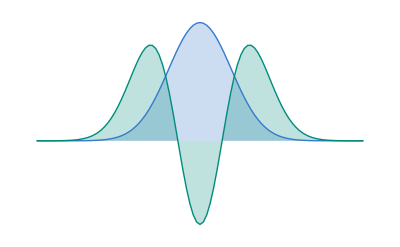
$dvrimg=
	Graphics[First@#,
		{
			ImageSize→{28,28},
			AspectRatio→Full,
			Method→{"ShrinkWrap"→True}
			}
		]&@-Graphics-;

Format[obj:dvrObjPattern?chemDVRValidQ]:=
	RawBoxes@
		BoxForm`ArrangeSummaryBox[
			"ChemDVRObject",
			obj,
			Replace[ChemDVRGet[obj,"Icon"],_Missing→$dvrimg],
				{
					BoxForm`MakeSummaryItem[{"Name: ",ChemDVRGet[obj,"Name"]},StandardForm],
					BoxForm`MakeSummaryItem[{"UUID: ",ChemDVRGet[obj,"UUID"]},StandardForm]
					},
			Block[{$ContextPath={"System`"}},
				Map[
					BoxForm`MakeSummaryItem[{Row@{#,": "},ChemDVRGet[obj,#]},StandardForm]&,{
						"Range",
						"Points",
						$dvrgr,
						$dvrke,
						$dvrpe,
						$dvrwf
					}]
				],
			StandardForm
			];

⌈ChemDVRClass⌋

⌈ChemDVRClass⌋

ChemDVRClasses[pat_:"*"]:=
	Map[
		FileBaseName,
		Join@@
			Map[
				FileNames[
					If[StringQ@pat,StringTrim[pat,".m"],pat]~~".m",
					#
					]&,
				ChemDVRDirectory["Classes", True]
				]
		];

(*PackageAddAutocompletions[
	"ChemDVRClass",
	List@ChemDVRClasses[]
	];*)

⌈Loading⌋

ChemDVRClass::noclass="No class template found at ``";
ChemDVRClass[f_String?(FileExistsQ)]:=
	With[{a=
		If[ExpandFileName[f]==
				ExpandFileName@ChemDVRFile["Classes",FileNameTake@f],
			ChemDVRNeeds@FileBaseName@f,
			ChemDVRNeeds@f
			]},
		If[AssociationQ@a,
			If[ExpandFileName[f]==
					ExpandFileName@ChemDVRFile["Classes",FileNameTake@f],
				ChemDVRClass[Append[a,"Class"->FileBaseName@f]],
				ChemDVRClass[a]
				],
			Message[ChemDVRClass::noclass,f];$Failed
			]
		];
ChemDVRClass[f_String?(Not@*FileExistsQ)]:=
	(If[FileExistsQ@#,
			ChemDVRClass@#,
			Message[ChemDVRClass::noclass,#];$Failed])&@
		ChemDVRFile["Classes",StringTrim[f,".m"]<>".m"];

⌈Instantiation⌋

ChemDVRClass[a_Association][ops___Rule]:=
	ChemDVRCreate[Join[a,<|ops|>]];
ChemDVRClass[a_Association][range:{{_?NumericQ,_?NumericQ}..}]:=
	ChemDVRClass[a]["Range"→range];
ChemDVRClass[a_Association][points:{__Integer?Positive}]:=
	ChemDVRClass[a]["Points"→points];
ChemDVRClass[a_Association][
	points:{__Integer?Positive},
	range:{{_?NumericQ,_?NumericQ}..}]:=
	ChemDVRClass[a]["Points"→points,"Range"→range];
ChemDVRClass[a_Association][
	range:{{_?NumericQ,_?NumericQ}..},
	points:{__Integer?Positive}
	]:=
	ChemDVRClass[a][points,range]

⌈Template⌋

$ChemDVRClassTemplate=
	With[{sn=ToBoxes@Placeholder["Name"]},
	Notebook[{
		Cell[
			TextData@{Cell[BoxData@ToBoxes@Placeholder["LongName"]]," ","DVR"}, 
			"CodeSection"],
		Cell[TextData@{Cell[BoxData@ToBoxes@Placeholder["Description"]]},"Text"],
		Cell[BoxData@"ChemDVRBegin[];","InputSection"];
		Cell[
			BoxData@{
				RowBox[{
					RowBox[{RowBox[{sn,"FormatGrid"}],"::","usage"}],"=",""""}],"
",
				RowBox[{
					RowBox[{RowBox[{sn,$dvrgr}],"::","usage"}],"=",""""}],"
",
				RowBox[{
					RowBox[{RowBox[{sn,$dvrke}],"::","usage"}],"=",""""}],"
",
				RowBox[{
					RowBox[{RowBox[{sn,"PotentialEnegy"}],"::","usage"}],"=",""""}],"
",
				RowBox[{
					RowBox[{RowBox[{sn,$dvrwf}],"::","usage"}],"=",""""}],"
",
				RowBox[{
					RowBox[{RowBox[{sn,"View"}],"::","usage"}],"=",""""}]
				},
				"CodeInput"],
		Cell[BoxData@RowBox[{RowBox[{"Begin","[",""`Private`"","]"}],";"}],
			"InputSection"],
		Cell["Grid Formatting Function", "CodeSubsubsection"],
		Cell[
			"This function should take a grid and the grid points used to generate the grid.",
			 "Text"],
		Cell[BoxData@
			RowBox[{
				RowBox[{RowBox[{sn,"FormatGrid"}],"[",RowBox[{"grid_",",","points_"}],"]"}],
				":=","
	",
				ToBoxes@Placeholder["FormatGrid Function"]}],
			"CodeInput"
			],
		Cell["Grid Function", "CodeSubsubsection"],
		Cell[
			"This function should take the number of grid points for each coordinate",
			 "Text"],
		Cell[BoxData@
			RowBox[{
				RowBox[{RowBox[{sn,$dvrgr}],"[",RowBox[{"points_",",","range_"}],"]"}],
				":=","
	",
				ToBoxes@Placeholder["Grid Function"]}],
			"CodeInput"
			],
		Cell["Kinetic Energy Function", "CodeSubsubsection"],
		Cell[
			"This should take the grid generated previously",
			 "Text"],
		Cell[BoxData@
			RowBox[{
				RowBox[{RowBox[{sn,$dvrke}],"[",RowBox[{"grid_"}],"]"}],
				":=","
	",
				ToBoxes@Placeholder["KineticEnergy Function"]}],
			"CodeInput"
			],
		Cell["Potential Energy Function", "CodeSubsubsection"],
		Cell[
			"This should take the grid generated previously",
			 "Text"],
		Cell[BoxData@
			RowBox[{
				RowBox[{RowBox[{sn,$dvrpe}],"[",RowBox[{"grid_"}],"]"}],
				":=","
	",
				ToBoxes@Placeholder["PotentialEnergy Function"]}],
			"CodeInput"
			],
		Cell["Wavefunctions Function", "CodeSubsubsection"],
		Cell[
			"This should take the kinetic and potential energies generated previously",
			 "Text"],
		Cell[BoxData@
			RowBox[{
				RowBox[{RowBox[{sn,$dvrwf}],"[",RowBox[{"T_","V_"}],"]"}],
				":=","
	",
				ToBoxes@Placeholder["Wavefunctions Function"]}],
			"CodeInput"
			],
		Cell["View Function", "CodeSubsubsection"],
		Cell[
			"This should take the wavefunctions, grid and potential energies",
			 "Text"],
		Cell[BoxData@
			RowBox[{
				RowBox[{RowBox[{sn,"View"}],"[",RowBox[{"wfs_","grid_","V_"}],"]"}],
				":=","
	",
				ToBoxes@Placeholder["View Function"]}],
			"CodeInput"
			],
		Cell[BoxData@RowBox[{RowBox[{"End","[","]"}],";"}],
			"InputSection"],
		Cell[
			BoxData@RowBox[{"<|","
","	",
				RowBox[{
					RowBox[{""Name"","→",RowBox@{""",ToBoxes@Placeholder["Name"],"""}}],
						",","
","	",
					RowBox[{""Dimension"","→",ToBoxes@Placeholder["Dimension"]}],
						",","
","	",
					RowBox[{""FormatGrid"","->",RowBox[{sn,"FormatGrid"}]}],
						",","
","	",
					RowBox[{""Grid"","->",RowBox[{sn,$dvrgr}]}],
						",","
","	",
					RowBox[{""KineticEnergy"","->",RowBox[{sn,$dvrke}]}],
						",","
","	",
					RowBox[{""PotentialEnergy"","->",RowBox[{sn,$dvrpe}]}],
						",","
","	",
					RowBox[{""Wavefunctions"","->",RowBox[{sn,$dvrwf}]}],
						",","
","	",
					RowBox[{""View"","->",RowBox[{sn,"View"}]}]}],
					"
","	","|>"}],
			"CodeInput"
			],
		Cell[BoxData@"ChemDVREnd[];","InputSection"],
		Cell["","SectionSeparator"]
		},
		StyleDefinitions→
			FrontEnd`FileName[{"ChemTools","Private"},"NewDVRClass.nb"]
		]
		];

⌈New⌋

Options[ChemDVRNewClass]={
	"LongName"→None,
	"Description"→None,
	"Name"→None,
	"Dimension"→None
	};
ChemDVRNewClass[ops:OptionsPattern[]]:=
	With[{
		name=
			Replace[OptionValue["Name"],
				s_String:>StringTrim[StringReplace[s,Except[WordCharacter]→""],"DVR"]<>
					"DVR"
				],
		ln=Replace[OptionValue["LongName"],None->OptionValue["Name"]],
		desc=OptionValue["Description"],
		dim=OptionValue["Dimension"]
		},
		With[{reps=
			{
				If[name===None,
					Nothing,
					Sequence@@{
						RowBox@{ToBoxes@Placeholder["Name"],s_}:>
							(name<>s),
						RowBox@{s1_,ToBoxes@Placeholder["Name"],s2_}:>
							s1<>name<>s2
						}
					],
				If[ln===None,
					Nothing,
					ToBoxes@Placeholder["LongName"]→ln
					],
				If[desc===None,
					Nothing,
					ToBoxes@Placeholder["Description"]→desc
					],
				If[dim===None,
					Nothing,
					ToBoxes@Placeholder["Dimension"]→dim
					]
				}
			},
			CreateDocument@
				If[Length@reps===0,
					$ChemDVRClassTemplate,
					If[name===None,
						ReplaceAll[$ChemDVRClassTemplate,reps],
						Append[ReplaceAll[$ChemDVRClassTemplate,reps],
							"WindowTitle"→name
							]
						]
				]
			]
		];

⌈Begin⌋

ChemDVRBegin[context_:""]:=
	If[$Context=!=Context[ChemDVRBegin],
		BeginPackage[Context[ChemDVRBegin]];
		$ContextPath=
			Join[$ContextPath, $PackageContexts]
		];

⌈End⌋

ChemDVREnd[]:=
	If[$Context===Context[ChemDVRBegin],
		EndPackage[]
		];

⌈Needs⌋

If[Not@AssociationQ@$ChemDVRLoaded,
	$ChemDVRLoaded=<|
		
		|>
	];

chemDVRGet[f_String?(FileExistsQ)]:=
	Block[{$ContextPath=Prepend[$PackageContexts, "System`"]},
		Replace[Get@f,
			{
				c_Association:>
					Set[$ChemDVRLoaded[f],
						Append[c,"File"→f]
						],
				_→$Failed
				}]
		];

ChemDVRNeeds[f_String?(FileExistsQ)]:=
	Lookup[$ChemDVRLoaded,f,
		chemDVRGet[f]
		];
ChemDVRNeeds[f_String?(Not@*FileExistsQ)]:=
	Lookup[$ChemDVRLoaded,f,
		Lookup[$ChemDVRLoaded,ChemDVRFile["Classes",StringTrim[f,".m"]<>".m"],
			chemDVRGet@ChemDVRFile["Classes",StringTrim[f,".m"]<>".m"]
			]
		];

⌈Reload⌋

ChemDVRReload[s_String]:=(
	If[KeyMemberQ[$ChemDVRLoaded,s],
		$ChemDVRLoaded[s]=.,
		$ChemDVRLoaded[ChemDVRFile["Classes",StringTrim[s,".m"]<>".m"]]=.
		];
	ChemDVRNeeds@s
	);

PackageAddAutocompletions[
	"ChemDVRReload",
	List@ChemDVRClasses[]
	];

⌈Formatting⌋

$dvrclassimg=
	Graphics[
		{
			Inset[
				Graphics[
					First@#/._Opacity→Opacity[.1],
					{
						ImageSize→{28,28},
						AspectRatio→Full,
						Method→{"ShrinkWrap"→True},
						PlotRange→{{-3,3},{-0,20}}
						}
					]
				],
			Inset[
				Graphics[
					{
						GrayLevel[.2],
						First@#2
						},
					{
						ImageSize→{28,28},
						AspectRatio→Full,
						Method→{"ShrinkWrap"→True}
						}
					]
				]
			},
		Background→GrayLevel[.95],
		FrameStyle→GrayLevel[.8],
		Frame→True,
		FrameTicks→False,
		ImageSize→{32,32}
		]&[$dvrimg,];

Format[ChemDVRClass[a_Association]]:=
	RawBoxes@
		BoxForm`ArrangeSummaryBox[
			"ChemDVRClass",
			Lookup[a,"Icon",ChemDVRClass@a],
			$dvrclassimg,
				{
					BoxForm`MakeSummaryItem[{"Name: ",Lookup[a,"Name"]},StandardForm]
					},
			KeyValueMap[
				BoxForm`MakeSummaryItem[{Row@{#,": "},#2},StandardForm]&,
					KeySelect[a,MatchQ[Except["Name"]]]
				],
			StandardForm
			];

End[];